```mathematica
(*Code to calculate semi-automatically the NLO Higgs-strahlung cross section in the real triplet model*)
(*Authors:
      Main authors: Cristian Sierra, cristian.sierra@cern.ch
                    Qin Yu,
       Contributors: Mohamed Sassi,
                     Anjan Barik,
                     Manuel Diaz*)
(*Date: 04-07-2025*)
```

## Load FeynCalc

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mohamed/Desktop/PostDocShanghai/HiggsNLO_OS/HiggsNLO-main/Models/Real_triplet/Calculator/Notebook

```mathematica
Global`$LoadAddOns={"FeynHelpers"};
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=0;
$CKM=True;
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True]
```

Successfully patched FeynArts.

# Higgsstrahlung@NLO

## Vertex Counterterms

```mathematica
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,MZ,mh];
```

```mathematica
TopoVertexCT=CreateCTTopologies[1,2->2,ExcludeTopologies->{TadpoleCTs ,WFCorrectionCTs, SelfEnergyCTs}];
VCTDiagZ=InsertFields[TopoVertexCT,{{-F[2,{1}],F[2,{1}]}}->{V[2],S[1]},Model->{"SM"},GenericModel-> {"Lorentz"},InsertionLevel->{Particles}, ExcludeParticles->{S[1], S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

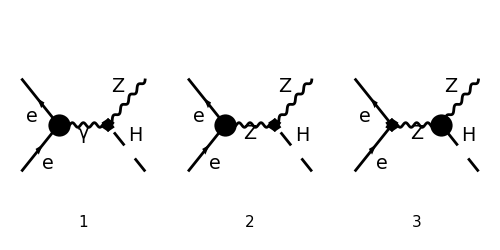

FeynArtsGraphics({e,e}→{Z,H})(([1] | [2] | [3]))

```mathematica
Paint[VCTDiagZ,ColumnsXRows->{3,1},ImageSize->{500,250}, Numbering->Simple]
```

```mathematica
topoLO1=CreateTopologies[0,2->2];
diagLO1=InsertFields[topoLO1,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"SM"},GenericModel->{"Lorentz"},InsertionLevel->{Particles},ExcludeParticles->{S[1], S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

```mathematica
ampLO1=FCFAConvert[CreateFeynAmp[diagLO1,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},TransversePolarizationVectors->{k1},ChangeDimension->D,Contract->True,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x]//FCGVToSymbol//DiracSimplify[#,DiracSubstitute67->False]&
```

-(ⅈ EL^2 MW (φ(-p1,ME)).(γ·ε^*(k1)).(γ̄)^6.(φ(p2,ME)))/(CW^3 ((k1+k2)^2-MZ^2))-(ⅈ EL^2 MW (φ(-p1,ME)).(γ·ε^*(k1)).(γ̄)^7.(φ(p2,ME)))/(CW^3 ((k1+k2)^2-MZ^2))+(ⅈ EL^2 MW (φ(-p1,ME)).(γ·ε^*(k1)).(γ̄)^7.(φ(p2,ME)))/(2 CW^3 SW^2 ((k1+k2)^2-MZ^2))

```mathematica
ComplexConjugate[ampLO1]
```

(ⅈ EL^2 MW (φ(p2,ME)).(γ̄)^7.(γ·ε(k1)).(φ(-p1,ME)))/(CW^3 ((k1+k2)^2-MZ^2))-(ⅈ EL^2 MW (1-2 SW^2) (φ(p2,ME)).(γ̄)^6.(γ·ε(k1)).(φ(-p1,ME)))/(2 CW^3 SW^2 ((k1+k2)^2-MZ^2))

```mathematica
ME = 0;

ampsCT=FCFAConvert[CreateFeynAmp[VCTDiagZ,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},ChangeDimension->D,Contract->True,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]/.FCGV[x_String]:>ToExpression[x]//FCGVToSymbol//DiracSimplify[#,DiracSubstitute67->False]&;
```

```mathematica
ampsCTSq[0]= 2ampsCT ( ComplexConjugate[ampLO1])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DiracSimplify//DoPolarizationSums[#,k1]&//FCReplaceD[#,D->4]&//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]& //DiracSimplify;
```

(2 dSW1 mh^2 MW^2 SW EL^4)/(CW^8 (MZ^2-s)^2)+(4 dSW1 MW^2 MZ^2 SW EL^4)/(CW^8 (MZ^2-s)^2)-(4 dSW1 MW^2 SW t EL^4)/(CW^8 (MZ^2-s)^2)+(dZZA1 MW^2 MZ^2 t EL^4)/(CW^5 (MZ^2-s)^2 s SW)+(2 dSW1 MW^2 t EL^4)/(CW^6 (MZ^2-s)^2 SW)+(dSW1 MW^2 t EL^4)/(2 CW^8 (MZ^2-s)^2 SW)-(dZAZ1 MW^2 t EL^4)/(CW^5 (MZ^2-s)^2 SW)-(dZZA1 MW^2 t EL^4)/(CW^5 (MZ^2-s)^2 SW)-(4 dZe1 MW^2 t EL^4)/(CW^6 (MZ^2-s)^2)-(dZH1 MW^2 t EL^4)/(CW^6 (MZ^2-s)^2)-(3 dZZZ1 MW^2 t EL^4)/(CW^6 (MZ^2-s)^2)-(dMWsq1 t EL^4)/(CW^6 (MZ^2-s)^2)+(2 dZe1 MW^2 t EL^4)/(CW^6 (MZ^2-s)^2 SW^2)+(dZH1 MW^2 t EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(3 dZZZ1 MW^2 t EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(dMWsq1 t EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(dZZA1 MW^2 MZ^2 t EL^4)/(4 CW^5 (MZ^2-s)^2 s SW^3)-(3 dSW1 MW^2 t EL^4)/(2 CW^6 (MZ^2-s)^2 SW^3)-(dSW1 MW^2 t EL^4)/(4 CW^8 (MZ^2-s)^2 SW^3)+(dZAZ1 MW^2 t EL^4)/(4 CW^5 (MZ^2-s)^2 SW^3)+(dZZA1 MW^2 t EL^4)/(4 CW^5 (MZ^2-s)^2 SW^3)-(dZe1 MW^2 t EL^4)/(2 CW^6 (MZ^2-s)^2 SW^4)-(dZH1 MW^2 t EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(3 dZZZ1 MW^2 t EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(dMWsq1 t EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(dSW1 MW^2 t EL^4)/(2 CW^6 (MZ^2-s)^2 SW^5)-(4 dSW1 MW^2 SW u EL^4)/(CW^8 (MZ^2-s)^2)+(2 dSW1 MW^2 SW t u EL^4)/(CW^8 MZ^2 (MZ^2-s)^2)-(dZZA1 MW^2 t u EL^4)/(2 CW^5 (MZ^2-s)^2 s SW)-(dSW1 MW^2 t u EL^4)/(CW^6 MZ^2 (MZ^2-s)^2 SW)-(dSW1 MW^2 t u EL^4)/(4 CW^8 MZ^2 (MZ^2-s)^2 SW)+(dZAZ1 MW^2 t u EL^4)/(2 CW^5 MZ^2 (MZ^2-s)^2 SW)+(dZZA1 MW^2 t u EL^4)/(2 CW^5 MZ^2 (MZ^2-s)^2 SW)+(2 dZe1 MW^2 t u EL^4)/(CW^6 MZ^2 (MZ^2-s)^2)+(dZH1 MW^2 t u EL^4)/(2 CW^6 MZ^2 (MZ^2-s)^2)+(3 dZZZ1 MW^2 t u EL^4)/(2 CW^6 MZ^2 (MZ^2-s)^2)+(dMWsq1 t u EL^4)/(2 CW^6 MZ^2 (MZ^2-s)^2)-(dZe1 MW^2 t u EL^4)/(CW^6 MZ^2 (MZ^2-s)^2 SW^2)-(dZH1 MW^2 t u EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^2)-(3 dZZZ1 MW^2 t u EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^2)-(dMWsq1 t u EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^2)+(dZZA1 MW^2 t u EL^4)/(8 CW^5 (MZ^2-s)^2 s SW^3)+(3 dSW1 MW^2 t u EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^3)+(dSW1 MW^2 t u EL^4)/(8 CW^8 MZ^2 (MZ^2-s)^2 SW^3)-(dZAZ1 MW^2 t u EL^4)/(8 CW^5 MZ^2 (MZ^2-s)^2 SW^3)-(dZZA1 MW^2 t u EL^4)/(8 CW^5 MZ^2 (MZ^2-s)^2 SW^3)+(dZe1 MW^2 t u EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^4)+(dZH1 MW^2 t u EL^4)/(16 CW^6 MZ^2 (MZ^2-s)^2 SW^4)+(3 dZZZ1 MW^2 t u EL^4)/(16 CW^6 MZ^2 (MZ^2-s)^2 SW^4)+(dMWsq1 t u EL^4)/(16 CW^6 MZ^2 (MZ^2-s)^2 SW^4)-(dSW1 MW^2 t u EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^5)+(dZZA1 MW^2 MZ^2 u EL^4)/(CW^5 (MZ^2-s)^2 s SW)+(2 dSW1 MW^2 u EL^4)/(CW^6 (MZ^2-s)^2 SW)+(dSW1 MW^2 u EL^4)/(2 CW^8 (MZ^2-s)^2 SW)-(dZAZ1 MW^2 u EL^4)/(CW^5 (MZ^2-s)^2 SW)-(dZZA1 MW^2 u EL^4)/(CW^5 (MZ^2-s)^2 SW)-(4 dZe1 MW^2 u EL^4)/(CW^6 (MZ^2-s)^2)-(dZH1 MW^2 u EL^4)/(CW^6 (MZ^2-s)^2)-(3 dZZZ1 MW^2 u EL^4)/(CW^6 (MZ^2-s)^2)-(dMWsq1 u EL^4)/(CW^6 (MZ^2-s)^2)+(2 dZe1 MW^2 u EL^4)/(CW^6 (MZ^2-s)^2 SW^2)+(dZH1 MW^2 u EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(3 dZZZ1 MW^2 u EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(dMWsq1 u EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(dZZA1 MW^2 MZ^2 u EL^4)/(4 CW^5 (MZ^2-s)^2 s SW^3)-(3 dSW1 MW^2 u EL^4)/(2 CW^6 (MZ^2-s)^2 SW^3)-(dSW1 MW^2 u EL^4)/(4 CW^8 (MZ^2-s)^2 SW^3)+(dZAZ1 MW^2 u EL^4)/(4 CW^5 (MZ^2-s)^2 SW^3)+(dZZA1 MW^2 u EL^4)/(4 CW^5 (MZ^2-s)^2 SW^3)-(dZe1 MW^2 u EL^4)/(2 CW^6 (MZ^2-s)^2 SW^4)-(dZH1 MW^2 u EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(3 dZZZ1 MW^2 u EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(dMWsq1 u EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(dSW1 MW^2 u EL^4)/(2 CW^6 (MZ^2-s)^2 SW^5)-(MW^2 t Conjugate[dZfL1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2)+(MW^2 t Conjugate[dZfL1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(MW^2 t Conjugate[dZfL1(2,1,1)] EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(MW^2 t u Conjugate[dZfL1(2,1,1)] EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2)-(MW^2 t u Conjugate[dZfL1(2,1,1)] EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^2)+(MW^2 t u Conjugate[dZfL1(2,1,1)] EL^4)/(16 CW^6 MZ^2 (MZ^2-s)^2 SW^4)-(MW^2 u Conjugate[dZfL1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2)+(MW^2 u Conjugate[dZfL1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(MW^2 u Conjugate[dZfL1(2,1,1)] EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(mh^2 MW^2 Conjugate[dZfL1(2,1,1)] EL^4)/(4 CW^6 (MZ^2-s)^2)+(MW^2 MZ^2 Conjugate[dZfL1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2)-(mh^2 MW^2 Conjugate[dZfL1(2,1,1)] EL^4)/(4 CW^6 (MZ^2-s)^2 SW^2)-(MW^2 MZ^2 Conjugate[dZfL1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(mh^2 MW^2 Conjugate[dZfL1(2,1,1)] EL^4)/(16 CW^6 (MZ^2-s)^2 SW^4)+(MW^2 MZ^2 Conjugate[dZfL1(2,1,1)] EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(MW^2 t Conjugate[dZfR1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2)+(MW^2 t u Conjugate[dZfR1(2,1,1)] EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2)-(MW^2 u Conjugate[dZfR1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2)+(mh^2 MW^2 Conjugate[dZfR1(2,1,1)] EL^4)/(4 CW^6 (MZ^2-s)^2)+(MW^2 MZ^2 Conjugate[dZfR1(2,1,1)] EL^4)/(2 CW^6 (MZ^2-s)^2)-(MW^2 t dZfL1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2)+(MW^2 t dZfL1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(MW^2 t dZfL1(2,1,1) EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(MW^2 t u dZfL1(2,1,1) EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2)-(MW^2 t u dZfL1(2,1,1) EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2 SW^2)+(MW^2 t u dZfL1(2,1,1) EL^4)/(16 CW^6 MZ^2 (MZ^2-s)^2 SW^4)-(MW^2 u dZfL1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2)+(MW^2 u dZfL1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(MW^2 u dZfL1(2,1,1) EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(mh^2 MW^2 dZfL1(2,1,1) EL^4)/(4 CW^6 (MZ^2-s)^2)+(MW^2 MZ^2 dZfL1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2)-(mh^2 MW^2 dZfL1(2,1,1) EL^4)/(4 CW^6 (MZ^2-s)^2 SW^2)-(MW^2 MZ^2 dZfL1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(mh^2 MW^2 dZfL1(2,1,1) EL^4)/(16 CW^6 (MZ^2-s)^2 SW^4)+(MW^2 MZ^2 dZfL1(2,1,1) EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(MW^2 t dZfR1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2)+(MW^2 t u dZfR1(2,1,1) EL^4)/(4 CW^6 MZ^2 (MZ^2-s)^2)-(MW^2 u dZfR1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2)+(mh^2 MW^2 dZfR1(2,1,1) EL^4)/(4 CW^6 (MZ^2-s)^2)+(MW^2 MZ^2 dZfR1(2,1,1) EL^4)/(2 CW^6 (MZ^2-s)^2)-(dZZA1 MW^2 MZ^4 EL^4)/(CW^5 (MZ^2-s)^2 s SW)-(dZZA1 mh^2 MW^2 MZ^2 EL^4)/(2 CW^5 (MZ^2-s)^2 s SW)-(dSW1 mh^2 MW^2 EL^4)/(CW^6 (MZ^2-s)^2 SW)-(dSW1 mh^2 MW^2 EL^4)/(4 CW^8 (MZ^2-s)^2 SW)+(dZAZ1 mh^2 MW^2 EL^4)/(2 CW^5 (MZ^2-s)^2 SW)+(dZZA1 mh^2 MW^2 EL^4)/(2 CW^5 (MZ^2-s)^2 SW)-(2 dSW1 MW^2 MZ^2 EL^4)/(CW^6 (MZ^2-s)^2 SW)-(dSW1 MW^2 MZ^2 EL^4)/(2 CW^8 (MZ^2-s)^2 SW)+(dZAZ1 MW^2 MZ^2 EL^4)/(CW^5 (MZ^2-s)^2 SW)+(dZZA1 MW^2 MZ^2 EL^4)/(CW^5 (MZ^2-s)^2 SW)+(dMWsq1 mh^2 EL^4)/(2 CW^6 (MZ^2-s)^2)+(2 dZe1 mh^2 MW^2 EL^4)/(CW^6 (MZ^2-s)^2)+(dZH1 mh^2 MW^2 EL^4)/(2 CW^6 (MZ^2-s)^2)+(3 dZZZ1 mh^2 MW^2 EL^4)/(2 CW^6 (MZ^2-s)^2)+(4 dZe1 MW^2 MZ^2 EL^4)/(CW^6 (MZ^2-s)^2)+(dZH1 MW^2 MZ^2 EL^4)/(CW^6 (MZ^2-s)^2)+(3 dZZZ1 MW^2 MZ^2 EL^4)/(CW^6 (MZ^2-s)^2)+(dMWsq1 MZ^2 EL^4)/(CW^6 (MZ^2-s)^2)-(dMWsq1 mh^2 EL^4)/(4 CW^6 (MZ^2-s)^2 SW^2)-(dZe1 mh^2 MW^2 EL^4)/(CW^6 (MZ^2-s)^2 SW^2)-(dZH1 mh^2 MW^2 EL^4)/(4 CW^6 (MZ^2-s)^2 SW^2)-(3 dZZZ1 mh^2 MW^2 EL^4)/(4 CW^6 (MZ^2-s)^2 SW^2)-(2 dZe1 MW^2 MZ^2 EL^4)/(CW^6 (MZ^2-s)^2 SW^2)-(dZH1 MW^2 MZ^2 EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(3 dZZZ1 MW^2 MZ^2 EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)-(dMWsq1 MZ^2 EL^4)/(2 CW^6 (MZ^2-s)^2 SW^2)+(dZZA1 MW^2 MZ^4 EL^4)/(4 CW^5 (MZ^2-s)^2 s SW^3)+(dZZA1 mh^2 MW^2 MZ^2 EL^4)/(8 CW^5 (MZ^2-s)^2 s SW^3)+(3 dSW1 mh^2 MW^2 EL^4)/(4 CW^6 (MZ^2-s)^2 SW^3)+(dSW1 mh^2 MW^2 EL^4)/(8 CW^8 (MZ^2-s)^2 SW^3)-(dZAZ1 mh^2 MW^2 EL^4)/(8 CW^5 (MZ^2-s)^2 SW^3)-(dZZA1 mh^2 MW^2 EL^4)/(8 CW^5 (MZ^2-s)^2 SW^3)+(3 dSW1 MW^2 MZ^2 EL^4)/(2 CW^6 (MZ^2-s)^2 SW^3)+(dSW1 MW^2 MZ^2 EL^4)/(4 CW^8 (MZ^2-s)^2 SW^3)-(dZAZ1 MW^2 MZ^2 EL^4)/(4 CW^5 (MZ^2-s)^2 SW^3)-(dZZA1 MW^2 MZ^2 EL^4)/(4 CW^5 (MZ^2-s)^2 SW^3)+(dMWsq1 mh^2 EL^4)/(16 CW^6 (MZ^2-s)^2 SW^4)+(dZe1 mh^2 MW^2 EL^4)/(4 CW^6 (MZ^2-s)^2 SW^4)+(dZH1 mh^2 MW^2 EL^4)/(16 CW^6 (MZ^2-s)^2 SW^4)+(3 dZZZ1 mh^2 MW^2 EL^4)/(16 CW^6 (MZ^2-s)^2 SW^4)+(dZe1 MW^2 MZ^2 EL^4)/(2 CW^6 (MZ^2-s)^2 SW^4)+(dZH1 MW^2 MZ^2 EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(3 dZZZ1 MW^2 MZ^2 EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)+(dMWsq1 MZ^2 EL^4)/(8 CW^6 (MZ^2-s)^2 SW^4)-(dSW1 mh^2 MW^2 EL^4)/(4 CW^6 (MZ^2-s)^2 SW^5)-(dSW1 MW^2 MZ^2 EL^4)/(2 CW^6 (MZ^2-s)^2 SW^5)

```mathematica
(*We can neglect the wave function renormalisation of the electrons, since they do not couple to BSM Higgs particles. No new BSM contributions. *)
```

```mathematica
AmplitudeSquaredCT=Simplify[ampsCTSq[0], Assumptions->{dZfL1[2, 1, 1]==0, dZfR1[2, 1, 1]==0}]//Simplify
```

1/(16 CW^8 s SW^5 (MZ^3-MZ s)^2)EL^4 (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) (-2 CW^3 MW^2 SW^2 (4 SW^2-1) (dZZA1 (MZ^2-s)-dZAZ1 s)+CW^2 s (SW (8 SW^4-4 SW^2+1) (dMWsq1+MW^2 (4 dZe1+dZH1+3 dZZZ1))-4 dSW1 MW^2 (4 SW^4-3 SW^2+1))+2 dSW1 MW^2 s SW^2 (16 SW^4-2 SW^2+1))

### Comparison with the paper:

```mathematica
deltacv = -1/(4*SW*CW)*(dZe1 + (SW^2-CW^2)/CW^2*dSW1/SW)+SW/CW*(dZe1 + 1/CW^2*dSW1/SW)+gv/2*dZZZ1 -1/2*dZAZ1;
deltaca = -1/(4*SW*CW)*(dZe1 + (SW^2-CW^2)/CW^2*dSW1/SW)+ga/2*dZZZ1;
firstterm = EL^4/(SW^2*CW^2)*(2*s*MZ^2 + t*u - mh^2*MZ^2)*(gv^2+ga^2)*(dZe1 + (2*SW^2-CW^2)/(CW^2)*dSW1/SW+1/2*dMWsq1/MW^2+1/2*dZH1+dZZZ1)/((s-MZ^2)^2)//Expand;
secondterm = EL^4/(SW^2*CW^2)*(2*s*MZ^2 + t*u - mh^2*MZ^2)*(gv*(s-MZ^2)*dZZA1/2)/(s*((s-MZ^2)^2 ) )//Expand;
```

```mathematica
thirdterm = EL^4/(SW^2*CW^2)*(2*s*MZ^2 + t*u - mh^2*MZ^2)*(deltacv*gv+ deltaca*ga)/((s-MZ^2)^2 )//Simplify;
```

```mathematica
PaperFormula = firstterm + secondterm + thirdterm;
```

```mathematica
PaperFormula //Simplify
```

1/(4 CW^5 MW^2 s SW^4 (MZ^2-s)^2)EL^4 (mh^2 MZ^2-2 MZ^2 s-t u) (-2 CW^3 SW (SW (dMWsq1 s (ga^2+gv^2)+MW^2 s (-dZAZ1 gv+2 dZe1 (ga^2+gv^2)+dZH1 (ga^2+gv^2)+3 dZZZ1 ga^2+3 dZZZ1 gv^2)+dZZA1 gv MW^2 (s-MZ^2))-2 dSW1 MW^2 s (ga^2+gv^2))+CW^2 MW^2 s (dZe1 SW (ga-4 gv SW^2+gv)-dSW1 (ga+gv))-8 CW dSW1 MW^2 s SW^3 (ga^2+gv^2)+dSW1 MW^2 s SW^2 (ga-3 gv))

```mathematica
Coefficient[AmplitudeSquaredCT-thirdterm-firstterm-secondterm, dZe1]//FullSimplify
```

(EL^4 (mh^2 MZ^2 (CW^3 MZ^2 SW (4 CW ga^2 SW+gv (4 SW (CW gv+SW)-1)-ga)+MW^2 (8 SW^4-4 SW^2+1))+CW^3 (-MZ^2) SW (4 CW ga^2 SW+gv (4 SW (CW gv+SW)-1)-ga) (2 MZ^2 s+t u)+MW^2 (8 SW^4-4 SW^2+1) (2 MZ^4-2 MZ^2 (t+u)+t u)))/(4 CW^6 SW^4 (MZ^3-MZ s)^2)

```mathematica
Coefficient[AmplitudeSquaredCT-thirdterm-firstterm-secondterm, dZZA1]//Simplify
```

(EL^4 (mh^2 (MW^2 MZ^2 (1-4 SW^2)-4 CW^3 gv MZ^4 SW)+4 CW^3 gv MZ^2 SW (2 MZ^2 s+t u)-MW^2 (4 SW^2-1) (2 MZ^4-2 MZ^2 (t+u)+t u)))/(8 CW^5 MZ^2 s SW^3 (MZ^2-s))

```mathematica
Coefficient[AmplitudeSquaredCT-thirdterm-firstterm-secondterm, dZH1]//Simplify
```

(EL^4 (mh^2 (8 CW^4 MZ^4 SW^2 (ga^2+gv^2)+MW^2 MZ^2 (8 SW^4-4 SW^2+1))-8 CW^4 MZ^2 SW^2 (ga^2+gv^2) (2 MZ^2 s+t u)+MW^2 (8 SW^4-4 SW^2+1) (2 MZ^4-2 MZ^2 (t+u)+t u)))/(16 CW^6 SW^4 (MZ^3-MZ s)^2)

```mathematica
Coefficient[AmplitudeSquaredCT, dZAZ1]//Simplify
```

(EL^4 MW^2 (4 SW^2-1) (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u))/(8 CW^5 SW^3 (MZ^3-MZ s)^2)

```mathematica
Coefficient[AmplitudeSquaredCT-thirdterm-firstterm-secondterm, dZZZ1]//Simplify
```

(3 EL^4 (mh^2 (8 CW^4 MZ^4 SW^2 (ga^2+gv^2)+MW^2 MZ^2 (8 SW^4-4 SW^2+1))-8 CW^4 MZ^2 SW^2 (ga^2+gv^2) (2 MZ^2 s+t u)+MW^2 (8 SW^4-4 SW^2+1) (2 MZ^4-2 MZ^2 (t+u)+t u)))/(16 CW^6 SW^4 (MZ^3-MZ s)^2)

```mathematica
Coefficient[AmplitudeSquaredCT-thirdterm-firstterm-secondterm, dSW1]//Simplify
```

1/(8 CW^8 SW^5 (MZ^3-MZ s)^2)EL^4 (-8 CW^6 MZ^2 SW^2 (ga^2+gv^2) (mh^2 MZ^2-2 MZ^2 s-t u)+2 CW^5 MZ^2 SW (ga+gv) (mh^2 MZ^2-2 MZ^2 s-t u)+16 CW^4 MZ^2 SW^4 (ga^2+gv^2) (mh^2 MZ^2-2 MZ^2 s-t u)-2 CW^3 MZ^2 SW^3 (ga-3 gv) (mh^2 MZ^2-2 MZ^2 s-t u)-2 CW^2 MW^2 (4 SW^4-3 SW^2+1) (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u)+MW^2 SW^2 (16 SW^4-2 SW^2+1) (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u))

```mathematica
Coefficient[AmplitudeSquaredCT-thirdterm-firstterm-secondterm, dMWsq1]//Simplify
```

(EL^4 (mh^2 (8 CW^4 MZ^4 SW^2 (ga^2+gv^2)+MW^2 MZ^2 (8 SW^4-4 SW^2+1))-8 CW^4 MZ^2 SW^2 (ga^2+gv^2) (2 MZ^2 s+t u)+MW^2 (8 SW^4-4 SW^2+1) (2 MZ^4-2 MZ^2 (t+u)+t u)))/(16 CW^6 MW^2 MZ^2 SW^4 (MZ^2-s)^2)

#### Checking that all UV divergences cancel in the vertex counterterms contributions

```mathematica
gv=Rationalize[(-1/2+2SW^2)/(2CW*SW)];
ga=Rationalize[(-1/(4CW*SW))];
```

```mathematica
(*Check of the first term in D.9 (2104.10709)*)
```

```mathematica
Test1 = dZe1 + (2*SW^2-CW^2)/(CW^2)*dSW1/SW+1/2*dMWsq1/MW^2+1/2*dZH1+dZZZ1 //Expand
```

(2 dSW1 SW)/CW^2+dMWsq1/(2 MW^2)-dSW1/SW+dZe1+dZH1/2+dZZZ1

```mathematica
Test1= Test1 /. Epsilon->eps;
Test1UVDiv = Coefficient[Test1, eps,-1]
Simplify[Test1UVDiv, SW^2+CW^2 == 1]
```

0

0

```mathematica
(*Check of the second term in D.9 (2104.10709)*)
```

```mathematica
Test2 = dZZA1//Expand
```

dZZA1

```mathematica
Test2= Test2 /. Epsilon->eps;
Test2UVDiv = Coefficient[Test2, eps,-1];
Simplify[Test2UVDiv, SW^2+CW^2 == 1]
```

0

```mathematica
(*Check of the third term in D.9 (2104.10709)*)
```

```mathematica
Test3 = deltacv*gv+ deltaca*ga //Expand;
Test3 = Test3 /. Epsilon->eps
Test3UVDiv = Coefficient[Test3, eps,-1]
Simplify[Test3UVDiv, SW^2+CW^2 == 1]
```

(3 dSW1 SW)/(4 CW^4)-dSW1/(8 CW^4 SW)-dSW1/(8 CW^2 SW^3)+dSW1/(4 CW^2 SW)+(dZe1 SW^2)/CW^2+dZe1/(8 CW^2 SW^2)-dZe1/(2 CW^2)+(dZZZ1 SW^2)/(2 CW^2)+dZZZ1/(16 CW^2 SW^2)-dZZZ1/(4 CW^2)-(dZAZ1 SW)/(2 CW)+dZAZ1/(8 CW SW)

0

0

```mathematica
Testdeltacv = deltacv/. Epsilon->eps//Expand;
TestDeltacvUVDiv = Coefficient[Testdeltacv, eps,-1];
Simplify[TestDeltacvUVDiv, SW^2+CW^2 == 1]
```

0

```mathematica
Testdeltaca = deltaca/. Epsilon->eps//Expand;
TestDeltacaUVDiv = Coefficient[Testdeltaca, eps,-1]
Simplify[TestDeltacaUVDiv, SW^2+CW^2 == 1]
```

0

0

## Self-energies

```mathematica
dZe1 = -1/2*(dZAA1 + SW/CW*dZZA1);
dSW1 = -1/2*CW^2/SW*(dMWsq1/MW^2-dMZsq1/MZ^2);
```

```mathematica
TopoCT=CreateCTTopologies[1,1->1,ExcludeTopologies->{TadpoleCTs ,WFCorrectionCTs}];
TopoΣ=CreateTopologies[1,1->1,ExcludeTopologies->{AllBoxes,Triangles, Tadpoles, WFCorrections}];
TransverseProjector=(1/3)(-Pair[LorentzIndex[ν],LorentzIndex[µ]]+(Pair[LorentzIndex[ν],Momentum[k]] Pair[LorentzIndex[µ],Momentum[k]]/Pair[Momentum[k],Momentum[k]]));
```

```mathematica
Me = 0;
ME = 0;
```

### H

```mathematica
ΣHHDiag=InsertFields[TopoΣ,{S[1]}->{S[1]},Model->{"tripletSM"},GenericModel->"tripletSM",InsertionLevel->{Particles},
ExcludeParticles->{S[1],V[1|2|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

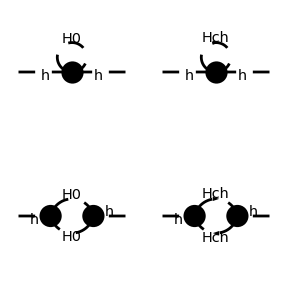

```mathematica
Paint[ΣHHDiag,ColumnsXRows->{2,2},Numbering->None];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

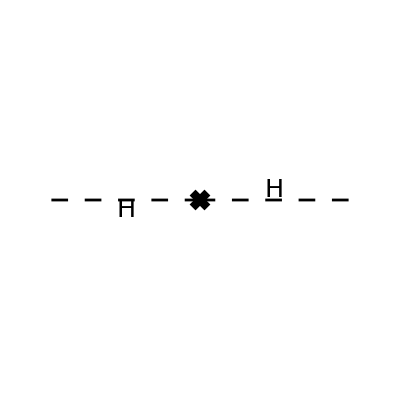

FeynArtsGraphics({H}→{H})(([]))

```mathematica
HHCTDiag=InsertFields[TopoCT,{S[1]}->{S[1]},Model->{"SM"},GenericModel->{"Lorentz"},InsertionLevel->{Particles}];
Paint[HHCTDiag,ColumnsXRows->{1,1},Numbering->None]
```

```mathematica
ΣHHAmp[0]=FCFAConvert[CreateFeynAmp[ΣHHDiag,PreFactor->1,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,LoopMomenta->{q},ChangeDimension->D,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

(3 λ3^2 v^2)/(2 (q^2-MH^2).((q-k)^2-MH^2))+(3 λ3)/(2 (q^2-MH^2))

```mathematica
(*When setting to True the following command rewrites A0 in terms of B0*)
```

```mathematica
SetOptions[A0,A0ToB0->False];
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣHHAmp[1]=  TID[ΣHHAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
ΣHH[0]=(-I)/(2 Pi)^4PaVeLimitTo4[ΣHHAmp[1]]//Expand//FullSimplify
```

(3 λ3 (λ3 v^2 B_0((k̄)^2,MH^2,MH^2)+A_0(MH^2)))/(32 π^2)

```mathematica
HHCTAmp[0]=FCFAConvert[CreateFeynAmp[HHCTDiag  ,PreFactor->-I,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//Expand//DiracSimplify
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

dZH1 (k̄)^2-dMHsq1-dZH1 MH^2

```mathematica
HHFullAmp[0] =ΣHH[0]+HHCTAmp[0]
```

(3 λ3 (λ3 v^2 B_0((k̄)^2,MH^2,MH^2)+A_0(MH^2)))/(32 π^2)+dZH1 (k̄)^2-dMHsq1-dZH1 MH^2

#### Renormalization in MSbar scheme

```mathematica
ΣHH[1]=ΣHH[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣHHat[0]=FCHideEpsilon[PaXEvaluate[ΣHH[1],PaXAnalytic->True]];
```

```mathematica
ΣHHat[1]=ΣHHat[0]-SMP["Delta"]*Coefficient[ΣHHat[0],SMP["Delta"]];
```

```mathematica
(* Derivative of  *)
```

```mathematica
DΣHHat[0]=D[ΣHHat[1],kSquare];
```

```mathematica
(*  at  *)
```

```mathematica
DΣHHatFormh2=DΣHHat[0]/.kSquare->mh^2;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(3 λ3^2 v^2 ((2 MH^2 log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/(2 MH^2)))/(√(mh^4-4 mh^2 MH^2))-1))/(32 π^2 mh^2)

```mathematica
ΣHHatFors=ΣHHat[1]/.kSquare->s;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(3 λ3 (s (log(μ^2/MH^2) (MH^2+λ3 v^2)-(MH^2 (-1+log(4)+2 log(π)))-2 λ3 v^2 (-1+log(2)+log(π)))+λ3 v^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2))))/(32 π^2 s)

#### Renormalization in OS scheme

```mathematica
ΣHH[1]=PaXEvaluate[ΣHH[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand
DΣHH[0]=D[ΣHH[1],kSquare];
```

(3 λ3^2 v^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(32 π^2 kSquare)+(3 λ3 MH^2)/(32 π^2 ε)+(3 λ3 MH^2 log(μ^2/MH^2))/(32 π^2)-(3 ℽ λ3 MH^2)/(32 π^2)+(3 λ3 MH^2)/(32 π^2)-(3 λ3 MH^2 log(π))/(32 π^2)+(3 λ3^2 v^2 log(μ^2/MH^2))/(32 π^2)+(3 λ3^2 v^2)/(32 π^2 ε)-(3 ℽ λ3^2 v^2)/(32 π^2)+(3 λ3^2 v^2)/(16 π^2)-(3 λ3^2 v^2 log(π))/(32 π^2)

```mathematica
%//FullSimplify//TraditionalForm
```

-(3 λ3^2 v^2 (√(kSquare (kSquare-4 MH^2))-2 MH^2 log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2))))/(32 π^2 kSquare √(kSquare (kSquare-4 MH^2)))

```mathematica
dMHsq1 = ΣHH[1]/.kSquare->mh^2//Simplify//Expand
```

(3 λ3^2 v^2 √(mh^4-4 mh^2 MH^2) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/(2 MH^2)))/(32 π^2 mh^2)+(3 λ3 MH^2)/(32 π^2 ε)+(3 λ3 MH^2 log(μ^2/MH^2))/(32 π^2)-(3 ℽ λ3 MH^2)/(32 π^2)+(3 λ3 MH^2)/(32 π^2)-(3 λ3 MH^2 log(π))/(32 π^2)+(3 λ3^2 v^2 log(μ^2/MH^2))/(32 π^2)+(3 λ3^2 v^2)/(32 π^2 ε)-(3 ℽ λ3^2 v^2)/(32 π^2)+(3 λ3^2 v^2)/(16 π^2)-(3 λ3^2 v^2 log(π))/(32 π^2)

```mathematica
dZH1 = -DΣHH[0]/.kSquare->mh^2//Simplify
```

(3 λ3^2 v^2 (√(mh^4-4 mh^2 MH^2)-2 MH^2 log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/(2 MH^2))))/(32 π^2 mh^2 √(mh^4-4 mh^2 MH^2))

```mathematica
PaXEvaluate[HHFullAmp[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand
```

(3 v^2 λ3^2 MH^4)/(8 mh^2 (mh-2 MH) (mh+2 MH) π^2)+(3 √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log((-mh^2+2 MH^2+√(mh^4-4 mh^2 MH^2))/MH^2) MH^4)/(16 mh^4 (mh-2 MH) (mh+2 MH) π^2)-(3 √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log(4) MH^4)/(32 mh^4 (mh-2 MH) (mh+2 MH) π^2)-(3 kSquare v^2 λ3^2 MH^2)/(8 mh^2 (mh-2 MH) (mh+2 MH) π^2)-(3 v^2 λ3^2 MH^2)/(32 (mh-2 MH) (mh+2 MH) π^2)-(3 √(kSquare (kSquare-4 MH^2)) v^2 λ3^2 log((2 MH^2-kSquare+√(kSquare (kSquare-4 MH^2)))/(2 MH^2)) MH^2)/(8 kSquare (mh-2 MH) (mh+2 MH) π^2)+(3 √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log((-mh^2+2 MH^2+√(mh^4-4 mh^2 MH^2))/MH^2) MH^2)/(8 mh^2 (mh-2 MH) (mh+2 MH) π^2)-(3 kSquare √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log((-mh^2+2 MH^2+√(mh^4-4 mh^2 MH^2))/MH^2) MH^2)/(16 mh^4 (mh-2 MH) (mh+2 MH) π^2)-(3 √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log(16) MH^2)/(32 mh^2 (mh-2 MH) (mh+2 MH) π^2)+(3 kSquare √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log(4) MH^2)/(32 mh^4 (mh-2 MH) (mh+2 MH) π^2)+(3 kSquare v^2 λ3^2)/(32 (mh-2 MH) (mh+2 MH) π^2)+(3 mh^2 √(kSquare (kSquare-4 MH^2)) v^2 λ3^2 log((2 MH^2-kSquare+√(kSquare (kSquare-4 MH^2)))/(2 MH^2)))/(32 kSquare (mh-2 MH) (mh+2 MH) π^2)-(3 √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log((-mh^2+2 MH^2+√(mh^4-4 mh^2 MH^2))/MH^2))/(32 (mh-2 MH) (mh+2 MH) π^2)+(3 √(mh^2 (mh^2-4 MH^2)) v^2 λ3^2 log(2))/(32 (mh-2 MH) (mh+2 MH) π^2)

```mathematica
%/.kSquare->mh^2//Simplify
```

(3 λ3^2 v^2 (mh^2-MH^2) (mh^4-4 mh^2 MH^2-2 MH^2 √(mh^4-4 mh^2 MH^2) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)+MH^2 log(4) √(mh^4-4 mh^2 MH^2)))/(32 π^2 mh^4 (mh^2-4 MH^2))

```mathematica
HHFullAmpRen=Re[PaXEvaluate[HHFullAmp[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]]//Expand
```

-1/(32 π^2)3 Re(1/(kSquare mh^4 (mh-2 MH) (mh+2 MH))λ3^2 v^2 (-kSquare^2 mh^4+4 kSquare^2 mh^2 MH^2-kSquare^2 MH^2 log(4) √(mh^2 (mh^2-4 MH^2))+2 kSquare^2 MH^2 √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)+mh^6 (-√(kSquare (kSquare-4 MH^2))) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2))+kSquare mh^4 MH^2+4 mh^4 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2))-4 kSquare mh^2 MH^4+kSquare mh^2 MH^2 log(16) √(mh^2 (mh^2-4 MH^2))+kSquare MH^4 log(4) √(mh^2 (mh^2-4 MH^2))+kSquare mh^4 √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)-kSquare mh^4 log(2) √(mh^2 (mh^2-4 MH^2))-4 kSquare mh^2 MH^2 √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)-2 kSquare MH^4 √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)))

```mathematica
HHFullAmpRen= HHFullAmpRen/.kSquare -> s
```

-1/(32 π^2)3 Re(1/(mh^4 s (mh-2 MH) (mh+2 MH))λ3^2 v^2 (mh^6 (-√(s (s-4 MH^2))) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2))+mh^4 MH^2 s+4 mh^4 MH^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2))-mh^4 s^2-4 mh^2 MH^4 s+4 mh^2 MH^2 s^2-MH^2 s^2 log(4) √(mh^2 (mh^2-4 MH^2))+mh^2 MH^2 s log(16) √(mh^2 (mh^2-4 MH^2))+MH^4 s log(4) √(mh^2 (mh^2-4 MH^2))+2 MH^2 s^2 √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)+mh^4 s √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)-mh^4 s log(2) √(mh^2 (mh^2-4 MH^2))-4 mh^2 MH^2 s √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)-2 MH^4 s √(mh^2 (mh^2-4 MH^2)) log((-mh^2+√(mh^4-4 mh^2 MH^2)+2 MH^2)/MH^2)))

### ZZ

```mathematica
ΣZZDiag=InsertFields[TopoΣ,{V[2]}->{V[2]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

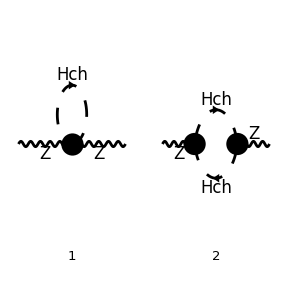

```mathematica
Paint[ΣZZDiag,ColumnsXRows->{2,1},Numbering->Simple];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

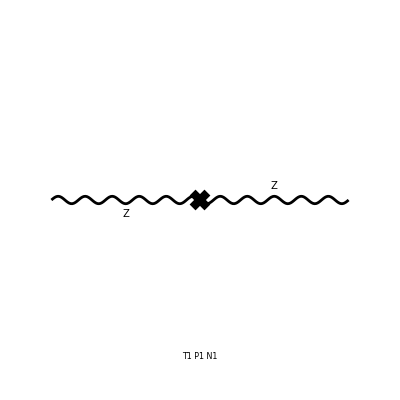

FeynArtsGraphics({Z}→{Z})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
ZZCTDiag=InsertFields[TopoCT,{V[2]}->{V[2]},Model->{"SM"},GenericModel->{"Lorentz"},InsertionLevel->{Particles}];
Paint[ZZCTDiag]
```

```mathematica
ΣZZAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣZZDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]//DiracSimplify//FCGVToSymbol;
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣZZAmp[1]= TID[ΣZZAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
SetOptions[A0,A0ToB0->True];
ΣZZ=(-I)/(2 Pi)^4PaVeLimitTo4[ΣZZAmp[1]]//ChangeDimension[#,4]&
```

-(ⅈ ((4 ⅈ π^2 CW^2 EL^2 MH^2 B_0(0,MH^2,MH^2) ((k̄)^ν (k̄)^µ-(k̄)^2 (ḡ)^νµ))/(3 SW^2 (k̄)^2)-(ⅈ π^2 CW^2 EL^2 (4 MH^2-(k̄)^2) ((k̄)^ν (k̄)^µ-(k̄)^2 (ḡ)^νµ) B_0((k̄)^2,MH^2,MH^2))/(3 SW^2 (k̄)^2)+(2 ⅈ π^2 CW^2 EL^2 ((k̄)^ν (k̄)^µ-(k̄)^2 (ḡ)^νµ))/(9 SW^2)))/(16 π^4)

```mathematica
(*Projecting out the transverse part, definition from hep-ph/0612057 Eq.50 ΣZZ= (-gµν+kµkν/k^2)ΣZZT + (kµkν/k^2) ΣZZL*)
```

```mathematica
ΣZZT[0]=Contract[TransverseProjector*ΣZZ]//Simplify
```

(CW^2 EL^2 (12 MH^2 (B_0(0,MH^2,MH^2)-B_0((k̄)^2,MH^2,MH^2))+(k̄)^2 (3 B_0((k̄)^2,MH^2,MH^2)+2)))/(144 π^2 SW^2)

```mathematica
(*ZZ counterterm*)
```

```mathematica
ZZCTAmp[0]=FCFAConvert[CreateFeynAmp[ZZCTDiag  ,PreFactor->-I,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

(dMZsq1+dZZZ1 MZ^2) (ḡ)^νµ-dZZZ1 (k̄)^2 (ḡ)^νµ+dZZZ1 (k̄)^ν (k̄)^µ

```mathematica
(*Projecting the transverse part of the counterterm*)
```

```mathematica
ZZCTAmpT[0]= Contract[TransverseProjector*ZZCTAmp[0]]//Simplify
```

dZZZ1 (k̄)^2-dMZsq1-dZZZ1 MZ^2

```mathematica
(*Full Amplitude including the counterterms*)
```

```mathematica
ZZTFullAmp[0] =ΣZZT[0]+ZZCTAmpT[0]
```

(CW^2 EL^2 (12 MH^2 (B_0(0,MH^2,MH^2)-B_0((k̄)^2,MH^2,MH^2))+(k̄)^2 (3 B_0((k̄)^2,MH^2,MH^2)+2)))/(144 π^2 SW^2)+dZZZ1 (k̄)^2-dMZsq1-dZZZ1 MZ^2

#### Renormalization in MSbar scheme

```mathematica
ΣZZT[1]=ΣZZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣZZTHat[0]=FCHideEpsilon[PaXEvaluate[ΣZZT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣZZTHat[1]=ΣZZTHat[0]-SMP["Delta"]*Coefficient[ΣZZTHat[0],SMP["Delta"]];
```

```mathematica
(*  at  and s *)
```

```mathematica
ΣZZTHatForMZ2=ΣZZTHat[1]/.kSquare->MZ^2;
```

```mathematica
ΣZZTHatFors=ΣZZTHat[1]/.kSquare->s;
```

```mathematica
(* Derivative of  *)
```

```mathematica
DΣZZTHat[0]=D[ΣZZTHat[1],kSquare];
```

```mathematica
(*  at  *)
```

```mathematica
DΣZZTHatforMZ2=DΣZZTHat[0]/.kSquare->MZ^2;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(CW^2 EL^2 (3 MZ^4 log(μ^2/MH^2)+12 MH^2 MZ^2+3 (2 MH^2+MZ^2) √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))-MZ^4 (-5+log(64)+6 log(π))))/(144 π^2 MZ^4 SW^2)

#### Renormalization in OS scheme

```mathematica
ΣZZT[1]=PaXEvaluate[ΣZZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Simplify
DΣZZT[0]=D[ΣZZT[1],kSquare];
%//FullSimplify//Expand//TraditionalForm
```

-(CW^2 EL^2 (kSquare (kSquare (ε (-8+3 ℽ+3 log(π))-3)-3 ε kSquare log(μ^2/MH^2)+24 ε MH^2)-(3 ε (kSquare (kSquare-4 MH^2))^(3/2) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/kSquare))/(144 π^2 ε kSquare SW^2)

(CW^2 EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(24 π^2 kSquare^2 SW^2)+(CW^2 EL^2 MH^2)/(12 π^2 kSquare SW^2)+(CW^2 EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2 kSquare SW^2)+(CW^2 EL^2 log(μ^2/MH^2))/(48 π^2 SW^2)+(CW^2 EL^2)/(48 π^2 ε SW^2)+(5 CW^2 EL^2)/(144 π^2 SW^2)-(ℽ CW^2 EL^2)/(48 π^2 SW^2)-(CW^2 EL^2 log(π))/(48 π^2 SW^2)

```mathematica
dMZsq1 = ΣZZT[1]/.kSquare->MZ^2//Simplify//Expand
dZZZ1 = -DΣZZT[0]/.kSquare->MZ^2//Simplify//Expand
```

(CW^2 EL^2 MZ^2 log(μ^2/MH^2))/(48 π^2 SW^2)+(CW^2 EL^2 √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(48 π^2 SW^2)-(CW^2 EL^2 MH^2 √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(12 π^2 MZ^2 SW^2)-(CW^2 EL^2 MH^2)/(6 π^2 SW^2)+(CW^2 EL^2 MZ^2)/(48 π^2 ε SW^2)+(CW^2 EL^2 MZ^2)/(18 π^2 SW^2)-(ℽ CW^2 EL^2 MZ^2)/(48 π^2 SW^2)-(CW^2 EL^2 MZ^2 log(π))/(48 π^2 SW^2)

-(CW^2 EL^2 MH^2)/(12 π^2 MZ^2 SW^2)-(CW^2 EL^2 √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(48 π^2 MZ^2 SW^2)-(CW^2 EL^2 MH^2 √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(24 π^2 MZ^4 SW^2)-(CW^2 EL^2 log(μ^2/MH^2))/(48 π^2 SW^2)-(CW^2 EL^2)/(48 π^2 ε SW^2)-(5 CW^2 EL^2)/(144 π^2 SW^2)+(ℽ CW^2 EL^2)/(48 π^2 SW^2)+(CW^2 EL^2 log(π))/(48 π^2 SW^2)

```mathematica
PaXEvaluate[ZZTFullAmp[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand ;
%/.kSquare->MZ^2//Simplify
```

0

```mathematica
(* Renormalized ZZ Self energy *)
```

```mathematica
ZZTFullAmpRen = Re[PaXEvaluate[ZZTFullAmp[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]]//Expand
```

1/(48 π^2)Re(1/(kSquare^2 MZ^4 SW^2)CW^2 EL^2 (-4 kSquare^3 MH^2 MZ^2-kSquare^3 MZ^2 √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))-2 kSquare^3 MH^2 √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))+kSquare^3 MZ^4+4 kSquare^2 MH^2 MZ^4+6 kSquare^2 MH^2 MZ^2 √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))-kSquare^2 MZ^6+MZ^4 (kSquare (kSquare-4 MH^2))^(3/2) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2))))

```mathematica
ZZTFullAmpRen/.kSquare->MZ^2//Simplify
```

0

```mathematica
ZZTFullAmpRen =ZZTFullAmpRen /.kSquare-> s
```

1/(48 π^2)Re(1/(MZ^4 s^2 SW^2)CW^2 EL^2 (4 MH^2 MZ^4 s^2+MZ^4 (s (s-4 MH^2))^(3/2) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2))-4 MH^2 MZ^2 s^3-MZ^2 s^3 √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))-2 MH^2 s^3 √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))+6 MH^2 MZ^2 s^2 √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2))+MZ^6 (-s^2)+MZ^4 s^3))

### γZ

```mathematica
ΣγZDiag=InsertFields[TopoΣ,{V[1]}->{V[2]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

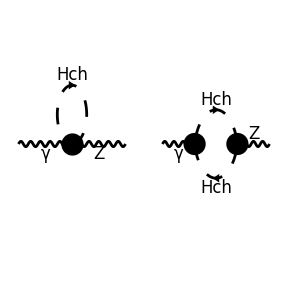

```mathematica
Paint[ΣγZDiag,ColumnsXRows->{2,1},Numbering->None];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

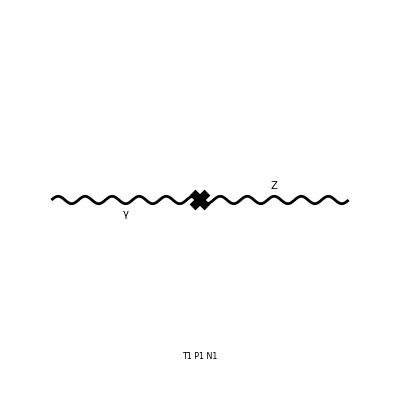

FeynArtsGraphics({\gamma}→{Z})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
γZCTDiag=InsertFields[TopoCT,{V[1]}->{V[2]},Model->{"SM"},GenericModel->{"Lorentz"},InsertionLevel->{Particles}];
Paint[γZCTDiag]
```

```mathematica
DiracSimplify[FCFAConvert[CreateFeynAmp[ΣγZDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]//DiracSimplify//FCGVToSymbol
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

-(gc11 gc38 q^µ (k-q)^ν)/((q^2-MH^2).((q-k)^2-MH^2))+(gc11 gc38 q^ν q^µ)/((q^2-MH^2).((q-k)^2-MH^2))-(gc11 gc38 (k-q)^ν (q-k)^µ)/((q^2-MH^2).((q-k)^2-MH^2))+(gc11 gc38 q^ν (q-k)^µ)/((q^2-MH^2).((q-k)^2-MH^2))+-(2 CW EL^2 g^νµ)/(SW (q^2-MH^2))

```mathematica
ΣγZAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣγZDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc11->FCGV["EL"]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]//DiracSimplify//FCGVToSymbol;
```

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣγZAmp[1]= TID[ΣγZAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
ΣγZ=(-I)/(2 Pi)^4PaVeLimitTo4[ΣγZAmp[1]];
```

```mathematica
(*Projecting out the transverse part*)
```

```mathematica
ΣγZT[0]=Contract[TransverseProjector*ΣγZ];
ΣγZT[0]//Simplify//TraditionalForm
```

(CW EL^2 (12 MH^2 (B_0(0,MH^2,MH^2)-B_0((k̄)^2,MH^2,MH^2))+(k̄)^2 (3 B_0((k̄)^2,MH^2,MH^2)+2)))/(144 π^2 SW)

```mathematica
(*γZ counterterm*)
```

```mathematica
γZCTAmp[0]=FCFAConvert[CreateFeynAmp[γZCTDiag  ,PreFactor->-I,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

-(k̄)^2 (dZAZ1/2+dZZA1/2) (ḡ)^νµ-(-dZAZ1/2-dZZA1/2) (k̄)^ν (k̄)^µ+1/2 dZZA1 MZ^2 (ḡ)^νµ

```mathematica
(*Projecting the transverse part of the counterterm*)
```

```mathematica
γZCTAmpT[0]= Contract[TransverseProjector*γZCTAmp[0]]//Simplify
```

1/2 ((k̄)^2 (dZAZ1+dZZA1)-dZZA1 MZ^2)

```mathematica
(*Full Amplitude including the counterterms*)
```

```mathematica
γZTFullAmp[0] =ΣγZT[0]+γZCTAmpT[0] //TraditionalForm//Expand
```

1/2 ((k̄)^2 (dZAZ1+dZZA1)-dZZA1 MZ^2)-(ⅈ (-(ⅈ π^2 CW EL^2 (4 MH^2-(k̄)^2) B_0((k̄)^2,MH^2,MH^2))/SW+(2 ⅈ π^2 CW EL^2 (k̄)^2)/(3 SW)+(4 ⅈ π^2 CW EL^2 MH^2 B_0(0,MH^2,MH^2))/SW))/(48 π^4)

#### Renormalization in MS bar scheme

```mathematica
ΣγZT[1]=ΣγZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣγZTHat[0]=FCHideEpsilon[PaXEvaluate[ΣγZT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣγZTHat[1]=ΣγZTHat[0]-SMP["Delta"]*Coefficient[ΣγZTHat[0],SMP["Delta"]];
```

```mathematica
(*  at 0 and s *)
```

```mathematica
ΣγZTHatFor0=ΣγZTHat[1]//Series[#,{kSquare,0,0}]&//Normal;
```

```mathematica
%//FullSimplify//TraditionalForm
```

0

```mathematica
ΣγZTHatFors=ΣγZTHat[1]/.kSquare->s//Expand
```

(CW EL^2 s log(μ^2/MH^2))/(48 π^2 SW)-(CW EL^2 MH^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2)))/(12 π^2 s SW)+(CW EL^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2)))/(48 π^2 SW)-(CW EL^2 MH^2)/(6 π^2 SW)+(CW EL^2 s)/(18 π^2 SW)-(CW EL^2 s log(4 π))/(48 π^2 SW)-(CW EL^2 s log(π))/(48 π^2 SW)

```mathematica
%//FullSimplify//TraditionalForm//Expand;
```

#### Renormalization in OS scheme

```mathematica
ΣγZT[1]=PaXEvaluate[ΣγZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Simplify//Expand
ΣγZTZero=PaXEvaluate[ΣγZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare/.kSquare->0,PaXAnalytic->True];
ΣγZTZeroanalytic=PaXEvaluate[ΣγZT[0],PaXAnalytic->True];
dZAZ1 = (-2*ΣγZT[1])/MZ^2/.kSquare->MZ^2//Simplify//Expand
dZZA1 = (2*ΣγZTZero)/MZ^2//Simplify//Expand
test=ΣγZT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare/.kSquare->0;
PaXEvaluate[test];
```

(CW EL^2 kSquare log(μ^2/MH^2))/(48 π^2 SW)-(CW EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(12 π^2 kSquare SW)+(CW EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2 SW)+(CW EL^2 kSquare)/(48 π^2 ε SW)+(CW EL^2 kSquare)/(18 π^2 SW)-(ℽ CW EL^2 kSquare)/(48 π^2 SW)-(CW EL^2 kSquare log(π))/(48 π^2 SW)-(CW EL^2 MH^2)/(6 π^2 SW)

(CW EL^2 MH^2)/(3 π^2 MZ^2 SW)-(CW EL^2 √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(24 π^2 MZ^2 SW)+(CW EL^2 MH^2 √(MZ^4-4 MH^2 MZ^2) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(6 π^2 MZ^4 SW)-(CW EL^2 log(μ^2/MH^2))/(24 π^2 SW)-(CW EL^2)/(24 π^2 ε SW)-(CW EL^2)/(9 π^2 SW)+(ℽ CW EL^2)/(24 π^2 SW)+(CW EL^2 log(π))/(24 π^2 SW)

0

```mathematica
γZTFullAmpRen= PaXEvaluate[ΣγZT[0]+γZCTAmpT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand ;
```

```mathematica
γZTFullAmpRen=γZTFullAmpRen/.kSquare-> s
```

(CW EL^2 MH^2 s)/(6 π^2 MZ^2 SW)-(CW EL^2 s √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(48 π^2 MZ^2 SW)+(CW EL^2 MH^2 s √(-MZ^2 (4 MH^2-MZ^2)) log((√(MZ^4-4 MH^2 MZ^2)+2 MH^2-MZ^2)/(2 MH^2)))/(12 π^2 MZ^4 SW)-(CW EL^2 MH^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2)))/(12 π^2 s SW)+(CW EL^2 √(s (s-4 MH^2)) log((√(s (s-4 MH^2))+2 MH^2-s)/(2 MH^2)))/(48 π^2 SW)-(CW EL^2 MH^2)/(6 π^2 SW)

```mathematica
γZTFullAmpRenZero=  ΣγZTZero+γZCTAmpT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare/.kSquare->0//Expand
```

0

```mathematica
dZZA1
```

0

### γγ

```mathematica
ΣγγDiag=InsertFields[TopoΣ,{V[1]}->{V[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[Except[6]],V[1|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

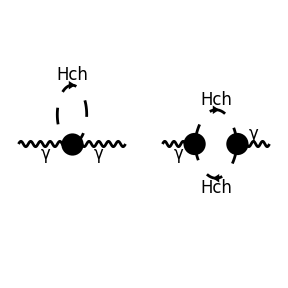

```mathematica
Paint[ΣγγDiag,ColumnsXRows->{2,1},Numbering->None];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

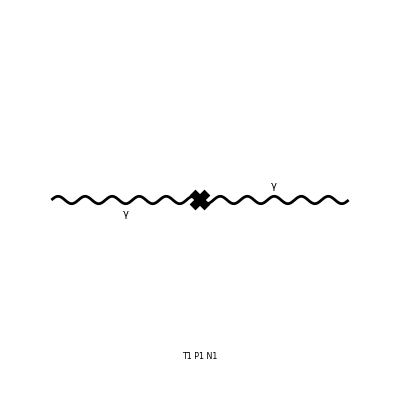

FeynArtsGraphics({\gamma}→{\gamma})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
γγCTDiag=InsertFields[TopoCT,{V[1]}->{V[1]},Model->{"SM"},GenericModel->{"Lorentz"},InsertionLevel->{Particles}];
Paint[γγCTDiag]
```

```mathematica
ΣγγAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣγγDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc11->FCGV["EL"]//DiracSimplify//FCGVToSymbol;
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣγγAmp[1]= TID[ΣγγAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
Σγγ=(-I)/(2 Pi)^4PaVeLimitTo4[ΣγγAmp[1]];
```

```mathematica
(*Projecting out the transverse part*)
```

```mathematica
ΣγγT[0]=Contract[TransverseProjector*Σγγ];
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 (2 ((k̄)^2+6 MH^2 B_0(0,MH^2,MH^2))+3 ((k̄)^2-4 MH^2) B_0((k̄)^2,MH^2,MH^2)))/(144 π^2)

```mathematica
(*γγ counterterm*)
```

```mathematica
γγCTAmp[0]=FCFAConvert[CreateFeynAmp[γγCTDiag  ,PreFactor->-I,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

dZAA1 (k̄)^ν (k̄)^µ-dZAA1 (k̄)^2 (ḡ)^νµ

```mathematica
(*Projecting the transverse part of the counterterm*)
```

```mathematica
γγCTAmpT[0]= Contract[TransverseProjector*γγCTAmp[0]]//Simplify
```

dZAA1 (k̄)^2

```mathematica
(*Full Amplitude including the counterterms*)
```

```mathematica
γγTFullAmp[0] =ΣγγT[0]+γγCTAmpT[0] //TraditionalForm//Expand//Simplify
```

((k̄)^2 (3 EL^2 B_0((k̄)^2,MH^2,MH^2)+2 (72 π^2 dZAA1+EL^2))+12 EL^2 MH^2 (B_0(0,MH^2,MH^2)-B_0((k̄)^2,MH^2,MH^2)))/(144 π^2)

#### Renormalization in MS bar scheme

```mathematica
ΣγγT[1]=ΣγγT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣγγTHat[0]=FCHideEpsilon[PaXEvaluate[ΣγγT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣγγTHat[1]=ΣγγTHat[0]-SMP["Delta"]*Coefficient[ΣγγTHat[0],SMP["Delta"]];
```

```mathematica
(* Derivative of  *)
```

```mathematica
DΣγγTHat[0]=D[ΣγγTHat[1],kSquare]
%//FullSimplify//Expand//TraditionalForm
```

(EL^2 (-3 kSquare^3 log(μ^2/MH^2)-8 kSquare^3+3 kSquare^3 log(4 π)+3 kSquare^3 log(π)+24 kSquare^2 MH^2-3 (kSquare (kSquare-4 MH^2))^(3/2) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2))))/(72 π^2 kSquare^3)-1/(144 π^2 kSquare^2)EL^2 (-9 kSquare^2 log(μ^2/MH^2)-24 kSquare^2+9 kSquare^2 log(4 π)+9 kSquare^2 log(π)+48 kSquare MH^2-(3 (kSquare (kSquare-4 MH^2))^(3/2) ((2 kSquare-4 MH^2)/(2 √(kSquare (kSquare-4 MH^2)))-1))/(√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)-9/2 √(kSquare (kSquare-4 MH^2)) (2 kSquare-4 MH^2) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))

(EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(24 π^2 kSquare^2)+(EL^2 MH^2)/(12 π^2 kSquare)+(EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2 kSquare)+(EL^2 log(μ^2/MH^2))/(48 π^2)+(5 EL^2)/(144 π^2)-(EL^2 log(π))/(24 π^2)-(EL^2 log(64))/(144 π^2)

```mathematica
(*  at 0 *)
```

```mathematica
DΣγγTHatFor0=DΣγγTHat[0]//Series[#,{kSquare,0,0}]&//Normal;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 log(μ^2/(4 π^2 MH^2)))/(48 π^2)

#### Renormalization in OS scheme

```mathematica
ΣγγT[1]=PaXEvaluate[ΣγγT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand
```

(EL^2 kSquare)/(48 π^2 ε)+(EL^2 kSquare log(μ^2/MH^2))/(48 π^2)-(EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(12 π^2 kSquare)+(EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2)-(ℽ EL^2 kSquare)/(48 π^2)+(EL^2 kSquare)/(18 π^2)-(EL^2 kSquare log(π))/(48 π^2)-(EL^2 MH^2)/(6 π^2)

```mathematica
ΣγγTZero[1]=ΣγγT[1]//Series[#,{kSquare,0,0}]&//Normal
```

0

```mathematica
DΣγγT[0]=D[ΣγγT[1],kSquare];
%//FullSimplify//Expand//TraditionalForm
```

EL^2/(48 π^2 ε)+(EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(24 π^2 kSquare^2)+(EL^2 MH^2)/(12 π^2 kSquare)+(EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2 kSquare)+(EL^2 log(μ^2/(π MH^2)))/(48 π^2)-(ℽ EL^2)/(48 π^2)+(5 EL^2)/(144 π^2)

```mathematica
DΣγγTZero= DΣγγT[0]//Series[#,{kSquare,0,0}]&//Normal//Simplify//Expand
```

EL^2/(48 π^2 ε)+(EL^2 log(μ^2/MH^2))/(48 π^2)-(ℽ EL^2)/(48 π^2)-(EL^2 log(π))/(48 π^2)

```mathematica
dZAA1 = -DΣγγTZero;
```

```mathematica
γγTFullAmpRen=ΣγγT[1] +γγCTAmpT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare //Expand
```

-(EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(12 π^2 kSquare)+(EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2)+(EL^2 kSquare)/(18 π^2)-(EL^2 MH^2)/(6 π^2)

```mathematica
γγTFullAmpRenZero = ΣγγTZero[1] +γγCTAmpT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare/.kSquare->0
```

0

### WW

```mathematica
ΣWWDiag=InsertFields[TopoΣ,{V[3]}->{V[3]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],V[1|2|3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

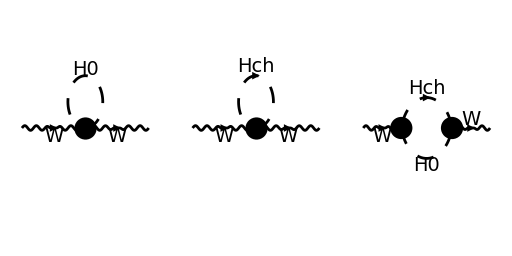

```mathematica
Paint[ΣWWDiag,ColumnsXRows->{3,1},Numbering->None,ImageSize->{512,256}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

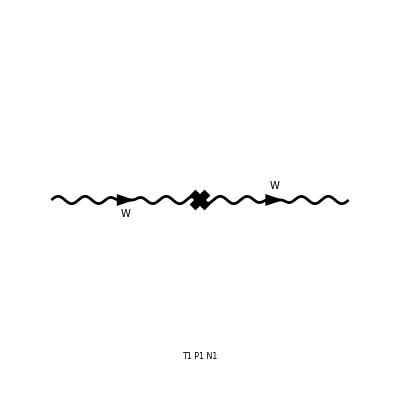

FeynArtsGraphics({W}→{W})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
WWCTDiag=InsertFields[TopoCT,{V[3]}->{V[3]},Model->{"SM"},GenericModel->{"Lorentz"},InsertionLevel->{Particles}];
Paint[WWCTDiag]
```

```mathematica
ΣWWAmp[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[ΣWWDiag,PreFactor->1,Truncated->True],IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},Contract->True,LoopMomenta->{q},ChangeDimension->D,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν},FinalSubstitutions->{MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x],DiracSubstitute67->True]/.gc28->(FCGV["EL"])/FCGV["SW"]/.gc24->-((FCGV["EL"])/FCGV["SW"])//DiracSimplify//FCGVToSymbol;
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

```mathematica
(*Tensor decomposition into Passarino Veltman functions:*)
```

```mathematica
ΣWWAmp[1]= TID[ΣWWAmp[0],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
ΣWW=(-I)/(2 Pi)^4PaVeLimitTo4[ΣWWAmp[1]];
ΣWWT[0]=Contract[TransverseProjector*ΣWW]//FullSimplify
```

(EL^2 (2 ((k̄)^2+6 MH^2 B_0(0,MH^2,MH^2))+3 ((k̄)^2-4 MH^2) B_0((k̄)^2,MH^2,MH^2)))/(144 π^2 SW^2)

```mathematica
(*WW counterterm*)
```

```mathematica
WWCTAmp[0]=FCFAConvert[CreateFeynAmp[WWCTDiag  ,PreFactor->-I,Truncated->True],
IncomingMomenta->{k},OutgoingMomenta->{k},TransversePolarizationVectors->{k},
Contract->True,
UndoChiralSplittings->True,List->False,DropSumOver->False,
LorentzIndexNames->{µ,ν},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.FCGV[x_String]:>ToExpression[x]//
DiracSimplify[#,DiracSubstitute67->True]&//FCGVToSymbol//DiracSimplify
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

(dMWsq1+dZW1 MW^2) (ḡ)^νµ-dZW1 (k̄)^2 (ḡ)^νµ+dZW1 (k̄)^ν (k̄)^µ

```mathematica
(*Projecting the transverse part of the counterterm*)
```

```mathematica
WWCTAmpT[0]= Contract[TransverseProjector*WWCTAmp[0]]//Simplify
```

dZW1 (k̄)^2-dMWsq1-dZW1 MW^2

```mathematica
(*Full Amplitude including the counterterms*)
```

```mathematica
WWTFullAmp[0] =ΣWWT[0]+WWCTAmpT[0]
```

(EL^2 (2 ((k̄)^2+6 MH^2 B_0(0,MH^2,MH^2))+3 ((k̄)^2-4 MH^2) B_0((k̄)^2,MH^2,MH^2)))/(144 π^2 SW^2)+dZW1 (k̄)^2-dMWsq1-dZW1 MW^2

#### Renormalization in MS bar scheme

```mathematica
ΣWWT[1]=ΣWWT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare;
```

```mathematica
ΣWWTHat[0]=FCHideEpsilon[PaXEvaluate[ΣWWT[1],PaXAnalytic->True]];
```

```mathematica
(* MS bar scheme *)
```

```mathematica
ΣWWTHat[1]=ΣWWTHat[0]-SMP["Delta"]*Coefficient[ΣWWTHat[0],SMP["Delta"]];
```

```mathematica
(*  at  *)
```

```mathematica
ΣWWTHatForMW2=ΣWWTHat[1]/.kSquare->MW^2;
```

```mathematica
%//FullSimplify//TraditionalForm
```

(EL^2 (3 MW^4 log(μ^2/(4 π^2 MH^2))+8 MW^2 (MW^2-3 MH^2)+3 (MW^2-4 MH^2) √(MW^4-4 MH^2 MW^2) log((√(MW^4-4 MH^2 MW^2)+2 MH^2-MW^2)/(2 MH^2))))/(144 π^2 MW^2 SW^2)

#### Renormalization in OS scheme

```mathematica
ΣWWT[1]=PaXEvaluate[ΣWWT[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand
```

(EL^2 kSquare log(μ^2/MH^2))/(48 π^2 SW^2)-(EL^2 MH^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(12 π^2 kSquare SW^2)+(EL^2 √(kSquare (kSquare-4 MH^2)) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/(48 π^2 SW^2)+(EL^2 kSquare)/(48 π^2 ε SW^2)-(ℽ EL^2 kSquare)/(48 π^2 SW^2)+(EL^2 kSquare)/(18 π^2 SW^2)-(EL^2 kSquare log(π))/(48 π^2 SW^2)-(EL^2 MH^2)/(6 π^2 SW^2)

```mathematica
DΣWWT[0]=D[ΣWWT[1],kSquare];
%//FullSimplify//Expand//TraditionalForm;
```

```mathematica
dMWsq1 = ΣWWT[1]/.kSquare->MW^2//Simplify//Expand;
dZW1 = -DΣWWT[0]/.kSquare->MW^2//Simplify//Expand;
```

```mathematica
WWTFullAmpRen = PaXEvaluate[WWTFullAmp[0]/.Pair[ Momentum[k], Momentum[k]]->kSquare,PaXAnalytic->True]//Expand //Simplify
```

(EL^2 ((MW^4 (kSquare (kSquare-4 MH^2))^(3/2) log((√(kSquare (kSquare-4 MH^2))-kSquare+2 MH^2)/(2 MH^2)))/kSquare+kSquare MW^2 (kSquare-MW^2) (MW^2-4 MH^2)+kSquare √(MW^4-4 MH^2 MW^2) (6 MH^2 MW^2-kSquare (2 MH^2+MW^2)) log((√(MW^4-4 MH^2 MW^2)+2 MH^2-MW^2)/(2 MH^2))))/(48 π^2 kSquare MW^4 SW^2)

```mathematica
WWTFullAmpRen/.kSquare-> MW^2//Simplify
```

0

```mathematica
dMWsq1= Re[dMWsq1];
dZW1 = Re[dZW1];
```

## Cross section

## LO

#### Amplitude

```mathematica
topoLO=CreateTopologies[0,2->2];
diagLO=InsertFields[topoLO,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

RuleDelayed::rhs: Pattern FeynArts`Initialize`i_ appears on the right-hand side of rule Index(FeynArts`Initialize`i_):>FeynArts`Initialize`i_.

General::stop: Further output of RuleDelayed::rhs will be suppressed during this calculation.

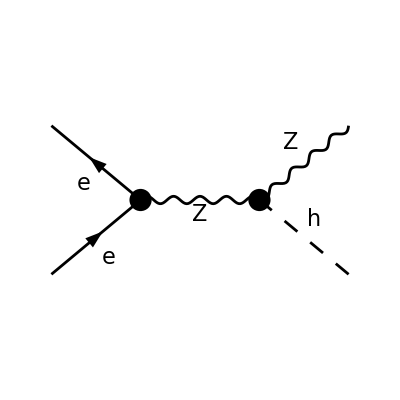

```mathematica
Paint[diagLO,ColumnsXRows->{1,1},Numbering->None,ImageSize->{256,256} ];
```

```mathematica
FCClearScalarProducts[];
```

```mathematica
(*set the kinematics*)
```

```mathematica
SetMandelstam[s,t,u,p1,p2,-k1,-k2,ME,ME,MZ,mh];
```

```mathematica
(*define the matrix element*)
(*PreFactor is set as -I so that ampLO[0]= instead of *)
```

```mathematica
ampLO[0]=FCFAConvert[CreateFeynAmp[diagLO,PreFactor->-I],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},TransversePolarizationVectors->{k1},ChangeDimension->D,Contract->True,UndoChiralSplittings->True,List->False,DropSumOver->False,LorentzIndexNames->{µ,ν}]//FCGVToSymbol//DiracSimplify[#,DiracSubstitute67->False]&;
```

```mathematica
(*Check by run following code commented out: The LO amplitude is the same as  in paper*)
```

```mathematica
(*ampLO[0]/.gc44->(EL^2*(v)/(2*CW^2*SW^2))/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.v->(2 SW CW MZ/EL)/.ME->0//DiracSimplify[#,DiracSubstitute67->True]&//FullSimplify*)
```

```mathematica
(*Matrix element squared. Spin average 1/4 is considered here. D dim -> 4 dim*)
```

```mathematica
ampLOSquared[0]=ampLO[0]( ComplexConjugate[ampLO[0]])//ChangeDimension[#,4]&//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]&//DoPolarizationSums[#,k1]&//TrickMandelstam[#,{s,t,u,2ME^2+MZ^2+mh^2}]& //DiracSimplify;
```

#### Matrix Element and cross section

```mathematica
(*LO matrix element squared. We set ME=0 here*)
```

```mathematica
MLO2aux=ampLOSquared[0]/.gc44->(EL^2*(v)/(2*CW^2*SW^2))/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.v->(2 SW CW MZ/EL)/.ME->0/.u->(MZ^2+mh^2-s-t)//Simplify
```

-(EL^4 (8 SW^4-4 SW^2+1) (mh^2 (MZ^2-t)-MZ^2 (2 s+t)+t (s+t)))/(16 CW^4 SW^4 (MZ^2-s)^2)

```mathematica
(*The differential cross section is given by  where  is the matrix element. We integrate over  and replace  from *)
```

```mathematica
MLO2[t_]:=Evaluate[MLO2aux]
```

```mathematica
σIntegrated=1/(16 Pi s^2)*Integrate[MLO2[t],t];
```

```mathematica
(*Källén function*)
 κ[x_,y_,z_]:=√(x^2+y^2+z^2-2x y-2x z-2y z);
(*Kinematic limits for the integration in terms of , see definition of the Mandelstam variable  and take *)
tUpper[s_]:=1/2 (MZ^2+mh^2-s+κ[s,MZ^2,mh^2]);
tLower[s_]:=1/2 (MZ^2+mh^2-s-κ[s,MZ^2,mh^2]);
```

```mathematica
(*LO cross section*)
σLOaux=(σIntegrated/.t->tUpper[s])- (σIntegrated/.t->tLower[s])//FullSimplify;
```

```mathematica
(*Eq.(3.2) in the paper, typo in paper, missing square in the κ inside the parenthesis*)
```

```mathematica
σLOliterature=(EL^4 (ga^2+gv^2) κ[s,MZ^2,mh^2] (12 MZ^2 s+κ[s,MZ^2,mh^2]^2))/(192 CW^2 π (MZ^2-s)^2 s^2 SW^2);
```

```mathematica
(*Validation*)
```

```mathematica
σLOaux==σLOliterature//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

## NLO

### Amplitude

```mathematica
LoopTopo=CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections,AllBoxes,SelfEnergies}];
```

```mathematica
LoopDiag=InsertFields[LoopTopo,{-F[2,{1}],F[2,{1}]}->{V[2],S[1]},Model->{"tripletSM"},GenericModel->{"tripletSM"},InsertionLevel->{Particles},ExcludeParticles->{S[1],S[2],V[3|4],U[1|2|3|4|11|12|31|32],F[_,{_}]}];
```

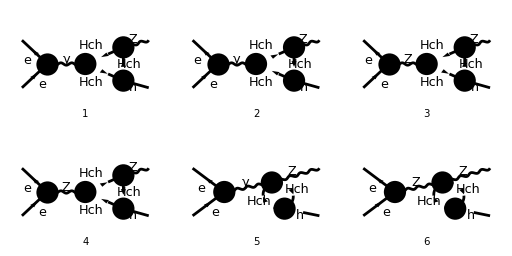

```mathematica
Paint[LoopDiag,ColumnsXRows->{3,2},Numbering->Simple,ImageSize->{512,256}];
```

```mathematica
(*PreFactor is set as -I so that ampsNLO[0]= instead of *)
```

```mathematica
ampsNLO[0]=FCFAConvert[CreateFeynAmp[LoopDiag,PreFactor->-I],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},TransversePolarizationVectors->{k1},ChangeDimension->D,UndoChiralSplittings->True,List->True,DropSumOver->False,LorentzIndexNames->{µ,ν,µ1,ν1,µ2,ν2},FinalSubstitutions->{lam3->λ3,MH0->MH,MHch->MH}]/.gc11->FCGV["EL"]/.gc38->(FCGV["CW"]*FCGV["EL"])/FCGV["SW"]/.gc47->-FCGV["EL"]//DiracSimplify[#,DiracSubstitute67->False]&//FCGVToSymbol;
```

```mathematica
(*Splitting the amplitudes into ZZ and γZ terms to simplify the analysis*)
```

```mathematica
ampsγZNLO[1]={ ampsNLO[0][[1]],ampsNLO[0][[2]],ampsNLO[0][[5]]};
```

```mathematica
ampsZZNLO[1]={ ampsNLO[0][[3]],ampsNLO[0][[4]],ampsNLO[0][[6]]};
```

```mathematica
(*Total of each contribution*)
```

```mathematica
ampsγZNLO[2] =Total[ampsγZNLO[1]];
```

```mathematica
ampsZZNLO[2] =Total[ampsZZNLO[1]];
```

### e + e - Z vertex contribution

#### Definitions

```mathematica
(*The LO amplitude without taking ME->0*)
```

```mathematica
AmpLO=ampLO[0]//DiracSimplify[#,DiracSubstitute67->False]&;
```

```mathematica
(*The NLO amplitude without taking ME->0, written in PaVe form*)
```

```mathematica
AmpNLOZZ=TID[ampsZZNLO[2],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*The following command allow us to use the Breitenlohner-Maison-’t Hooft-Veltman scheme when dealing with matrices in D dimensions, in particular to handle gamma5*)
```

```mathematica
FCSetDiracGammaScheme["BMHV"];
```

```mathematica
(*Product aiming to get Eq. 3.8 in D dimension, notice *)
```

```mathematica
ampsquaredZZ=(AmpNLOZZ ComplexConjugate[AmpLO]+AmpLO ComplexConjugate[AmpNLOZZ])/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.gc44->(EL^2*v)/(2*CW^2*SW^2)//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]& //DoPolarizationSums[#,k1]&;
```

```mathematica
(*D dim -> 4 dim, take ME->0*)
(*Notice: //PaVeLimitTo4[(1/(2Pi)^4)*#]& is equal to //FCReplaceD[(1/(2Pi)^D)*#,D->4-2Epsilon]&//Series[#,{Epsilon,0,0}]&//Normal*)
(*Notice: ME->0 should be taken after DiracSimplify because it leads to new terms with ME*)
```

```mathematica
TwoReampZZ=1/(2Pi)^4(PaVeLimitTo4[ampsquaredZZ]//DiracSimplify)/.ME->0//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&;
```

```mathematica
(*The resultant expression is given in terms of tensor PaVe functions*)
```

```mathematica
TwoReampZZ//FullSimplify//TraditionalForm
```

1/(128 π^2 CW^2 MZ^2 SW^6 (MZ^2-s)^2)EL^6 λ3 (8 SW^4-4 SW^2+1) v^2 (2 (2 (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) C_00(mh^2,MZ^2,s,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) C_1(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) (C_11(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+C_12(mh^2,s,MZ^2,MH^2,MH^2,MH^2)))-(mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) B_0(mh^2,MH^2,MH^2))

```mathematica
(*We can look at the PaVe part alone by take out the factor of TwoReampZZ*)
```

```mathematica
factorPavepartZZaux=1/(16 MZ^2  π^2 SW^4(MZ^2-s)^2) EL^6 λ3 v^2(ga^2+gv^2);
```

```mathematica
(*Writing down the Pavepart in terms of scalars PaVe functions A0,B0,C0 with the //PaVeReduce command:*)
```

```mathematica
PavepartZZaux=(factorPavepartZZaux )^-1 TwoReampZZ/.u->MZ^2+mh^2-s-t//PaVeReduce;
```

```mathematica
(*Use //PaVeLimitTo4 again because //PaVeReduce works in D dim. The 1/(2Pi)^4 is set before*)
```

```mathematica
PavepartZZ=PaVeLimitTo4[PavepartZZaux]//Contract;
```

#### Literature expression from Eq . (3.8) and C .8 in the paper

```mathematica
(*Let's do the general case*)
```

```mathematica
C22s=(1/(2*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))^2))*(2*Mz^2*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))-6*Mz^2*(Mz^2*(Mh^2-Mz^2+s)+(M1^2-M2^2)*(Mh^2+Mz^2-s))*PaVe[0,{MZ^2},{MH^2,MH^2}]-(Mh^6+(Mz^2-s)^2*(3*Mz^2-s)-Mh^4*(5*Mz^2+3*s)+Mh^2*(Mz^4+3*s^2)-2*(M1^2-M2^2)*(Mh^4+Mh^2*(4*Mz^2-s)+(Mz^2-s)^2))*PaVe[0,{mh^2},{MH^2,MH^2}]+((Mh^2-3*Mz^2)*(Mh^2-Mz^2)^2-(3*Mh^4+Mz^4)*s+(3*Mh^2+5*Mz^2)*s^2-s^3+(1/s)*(M1^2-M2^2)*((Mh^2-Mz^2)^3-5*(Mh^4-Mz^4)*s+(7*Mh^2-Mz^2)*s^2-3*s^3))*PaVe[0,{s},{MH^2,MH^2}]+2*(Mz^4*(Mh^4-2*Mh^2*(Mz^2-2*s)+(Mz^2-s)^2(*this square is missing in the paper*))+(M1^4+M2^4)*(Mh^4+2*Mh^2*(2*Mz^2-s)+(Mz^2-s)^2)-2*Mz^2*(Mh^4*(-2*M1^2+M2^2)+(Mz^2-s)^2*(M1^2-2*M2^2)+Mh^2*(Mz^2+s)*(M1^2+M2^2))-2*M1^2*M2^2*(Mh^4+2*Mh^2*(2*Mz^2-s)+(Mz^2-s)^2))*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
C23s=(1/(2*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))^2))*((Mh^2+Mz^2-s)*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))+(Mz^2*(-Mh^4+5*(Mz^2-s)^2-4*Mh^2*(Mz^2+s))-(M1^2-M2^2)*(Mh^4+(Mz^2-s)^2+2*Mh^2*(5*Mz^2-s)))*PaVe[0,{MZ^2},{MH^2,MH^2}]-((Mh^6+2*(Mz^2-s)^3-2*Mh^4*(3*Mz^2+2*s)+Mh^2*(3*Mz^4-8*Mz^2*s+5*s^2))-6*(M1^2-M2^2)*Mh^2*(Mh^2+Mz^2-s))*PaVe[0,{mh^2},{MH^2,MH^2}]+((Mh^6-(Mz^2-s)^2*(3*Mz^2+2*s)-Mh^4*(5*Mz^2+4*s)+Mh^2*(7*Mz^4-4*Mz^2*s+5*s^2))+(M1^2-M2^2)*((Mh^2-Mz^2)^2+2*(-3*Mh^4+Mh^2*Mz^2+2*Mz^4)*s+(3*Mh^2-5*Mz^2)*s^2+2*s^3))*PaVe[0,{s},{MH^2,MH^2}]+2*((Mz^2*((Mz^2-s)^3+Mh^4*(Mz^2+2*s)-Mh^2*(2*Mz^4-3*Mz^2*s+(*there is a wrong extra factor of 2 here in the paper*)s^2)))+3*(M1^4+M2^4)*Mh^2*(Mh^2+Mz^2-s)+M1^2*(Mh^2-Mz^2+s)*(Mh^4+2*Mh^2*(2*Mz^2-s)+(Mz^2-s)^2)+2*M2^2*((Mz^2-s)^3-Mh^4*(2*Mz^2+s)+Mh^2*(Mz^4-3*Mz^2*s+2*s^2))-6*M1^2*M2^2*Mh^2*(Mh^2+Mz^2-s))*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
C24s=(1/(4*(Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))))*((Mh^4+(Mz^2-s)^2-2*Mh^2*(Mz^2+s))-(Mz^2*(Mh^2-Mz^2+s)+(M1^2-M2^2)*(Mh^2+Mz^2-s))*PaVe[0,{MZ^2},{MH^2,MH^2}]+Mh^2*(Mh^2-Mz^2-s+2*M1^2-2*M2^2)*PaVe[0,{mh^2},{MH^2,MH^2}]+(s*(-Mh^2-Mz^2+s)-(M1^2-M2^2)*(Mh^2-Mz^2+s))*PaVe[0,{s},{MH^2,MH^2}]+(2*(Mh^2*Mz^2*s+(M1^4+M2^4)*Mh^2+M1^2*Mh^2*(Mh^2-Mz^2-s)+M2^2*((Mz^2-s)^2-Mh^2*(Mz^2+s))-2*M1^2*M2^2*Mh^2))*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
(*The factor of part from eq 3.8 with only PaVe functions, including spin average 1/4 and the sum factor 2*)
```

```mathematica
factorPavepartliterature=-1/4*2*1/(16 π^2)(4 EL^3)/(MZ SW CW)(gv^2+ga^2)/((s-MZ^2)^2)(-lam3*v)(- gc38)^2/.lam3->λ3/.gc38->(CW*EL)/SW/.v->(2 SW CW MZ/EL)//FullSimplify;
```

```mathematica
(*Part from eq 3.8 with only PaVe functions*)
```

```mathematica
Pavepartliterature=2((t u +2s MZ^2 -mh^2MZ^2)(2C24s-1/2 PaVe[0,{mh^2},{MH^2,MH^2}])+(s+MZ^2-mh^2)(mh^2MZ^2-t u)(C22s-C23s))/.Mz->MZ/.Mh->mh/.M1->MH/.M2->MH;
```

#### Validation with the literature

```mathematica
(*Factor matching*)
```

```mathematica
factorPavepartliterature==factorPavepartZZaux/.v->(2 SW CW MZ/EL)//Simplify
```

True

```mathematica
(*B0(s) matching *)
```

```mathematica
Coefficient[Pavepartliterature, PaVe[0,{s},{MH^2,MH^2}]]==Coefficient[PavepartZZ, PaVe[0,{s},{MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&//Simplify
```

True

```mathematica
(*B0(k2) matching*)
```

```mathematica
Coefficient[Pavepartliterature, PaVe[0,{mh^2},{MH^2,MH^2}]]==Coefficient[PavepartZZ, PaVe[0,{mh^2},{MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

```mathematica
(*B0(k1) matching*)
```

```mathematica
Coefficient[Pavepartliterature, PaVe[0,{MZ^2},{MH^2,MH^2}]]==Coefficient[PavepartZZ, PaVe[0,{MZ^2},{MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

```mathematica
(*C0(k1,k2) matching *)
```

```mathematica
Coefficient[Pavepartliterature,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]==Coefficient[PavepartZZ,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

```mathematica
(*Independent term from the literature*)
```

```mathematica
Indtermliterature= Pavepartliterature-(Coefficient[Pavepartliterature, PaVe[0,{s},{MH^2,MH^2}]]* PaVe[0,{s},{MH^2,MH^2}]+Coefficient[Pavepartliterature, PaVe[0,{MZ^2},{MH^2,MH^2}]]* PaVe[0,{MZ^2},{MH^2,MH^2}]+Coefficient[Pavepartliterature, PaVe[0,{mh^2},{MH^2,MH^2}]]* PaVe[0,{mh^2},{MH^2,MH^2}]+Coefficient[Pavepartliterature,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
(*Independent term from the code*)
```

```mathematica
Indterm= PavepartZZ-(Coefficient[PavepartZZ,PaVe[0,{s},{MH^2,MH^2}]]* PaVe[0,{s},{MH^2,MH^2}]+Coefficient[PavepartZZ,PaVe[0,{MZ^2},{MH^2,MH^2}]]* PaVe[0,{MZ^2},{MH^2,MH^2}]+Coefficient[PavepartZZ,PaVe[0,{mh^2},{MH^2,MH^2}]]* PaVe[0,{mh^2},{MH^2,MH^2}]+Coefficient[PavepartZZ,PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]]*PaVe[0,{mh^2,MZ^2,s},{MH^2,MH^2,MH^2}]);
```

```mathematica
(*Independent term matching *)
```

```mathematica
Indtermliterature==Indterm//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&
```

True

### e + e - γ vertex contribution

```mathematica
AmpNLOγZ=TID[ampsγZNLO[2],q,UsePaVeBasis->True,ToPaVe->True]//DiracSimplify;
```

```mathematica
(*Product aiming to get Eq. 3.8 in D dimension*)
```

```mathematica
ampsquaredγZ=(AmpNLOγZ ComplexConjugate[AmpLO]+AmpLO ComplexConjugate[AmpNLOγZ])/.gc54L->(gv+ga) EL/.gc54R->(gv-ga) EL/.gc44->(EL^2*v)/(2*CW^2*SW^2)//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/2^2]& //DoPolarizationSums[#,k1]&;
```

```mathematica
(*D dim -> 4 dim, take ME->0*)
```

```mathematica
TwoReampγZ=(1/(2Pi)^4)*(PaVeLimitTo4[ampsquaredγZ]//DiracSimplify)/.ME->0//TrickMandelstam[#,{s,t,u,MZ^2+mh^2}]&;
```

```mathematica
(*The resultant expression is given in terms of tensor PaVe functions, this validates the earlier identification in the paper of the PaVe part of the expression factorizing from both contributions*)
```

```mathematica
TwoReampγZ//FullSimplify//TraditionalForm
```

1/(64 π^2 CW^2 MZ^2 s SW^4 (MZ^2-s))EL^6 λ3 (4 SW^2-1) v^2 (2 (2 (mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) C_00(mh^2,MZ^2,s,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) C_1(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+(2 MZ^2-t-u) (mh^2 MZ^2-t u) (C_11(mh^2,s,MZ^2,MH^2,MH^2,MH^2)+C_12(mh^2,s,MZ^2,MH^2,MH^2,MH^2)))-(mh^2 MZ^2+2 MZ^4-2 MZ^2 (t+u)+t u) B_0(mh^2,MH^2,MH^2))

### Renormalized propagator

```mathematica
MWHat2=MW^2+Re[ΣWWTHatForMW2];
MZHat2=MZ^2+Re[ΣZZTHatForMZ2];
cHat=√(MWHat2/MZHat2);
sHat=√(1-cHat^2);
ELHat=EL(1-1/2 δZγγHat-1/2 sHat/cHat δZZγHat);
IWe3=-1/2;
Qe=-1;
gveff=(IWe3-2κHat sHat^2 Qe)/(2 sHat cHat);
gaeff=IWe3/(2 sHat cHat);
κHat=1-cHat/sHat ΣγZTHatFors/s;
ΓZMZ=Im[ΣZZTHatFors];
δZZZHat=-Re[DΣZZTHatforMZ2];
δZhHat=-Re[DΣHHatFormh2];
δZγγHat=-Re[DΣγγTHatFor0];
δZZγHat=2 ΣγZTHatFor0/MZ^2;
```

```mathematica
ρHat=1/(s-MZ^2+I ΓZ*MZ)(1+(Re[ΣZZTHatForMZ2]-Re[ΣZZTHatFors])/(s-MZ^2)+1/2 δZZZHat-1/2 Re[DΣHHatFormh2])/.v->(2 SW CW MZ/EL);
```

### OS CT

```mathematica
VertexOS = PaperFormula//Expand;
VertexOS = VertexOS /. Epsilon->(1/eps) //Expand;
VertexUVDivOS = Coefficient[VertexOS, eps,1]
Simplify[VertexUVDivOS, SW^2+CW^2 == 1]
PaperFormula = VertexOS/.eps-> 0;
```

(MZ^2 s EL^6)/(48 CW^4 π^2 (MZ^2-s)^2)+(t u EL^6)/(96 CW^4 π^2 (MZ^2-s)^2)+(t u EL^6)/(96 CW^4 π^2 (s-MZ^2)^2)+(t u EL^6)/(96 CW^2 π^2 (MZ^2-s)^2 SW^2)-(t u EL^6)/(192 CW^4 π^2 (MZ^2-s)^2 SW^2)-(t u EL^6)/(192 CW^4 π^2 (s-MZ^2)^2 SW^2)+(t u EL^6)/(128 CW^2 π^2 (MZ^2-s)^2 SW^4)+(t u EL^6)/(768 CW^4 π^2 (MZ^2-s)^2 SW^4)+(t u EL^6)/(768 CW^4 π^2 (s-MZ^2)^2 SW^4)-(t u EL^6)/(96 π^2 (s-MZ^2)^2 SW^4)-(t u EL^6)/(384 CW^2 π^2 (MZ^2-s)^2 SW^6)+(t u EL^6)/(384 π^2 (MZ^2-s)^2 SW^6)+(t u EL^6)/(192 π^2 (s-MZ^2)^2 SW^6)-(t u EL^6)/(768 π^2 (MZ^2-s)^2 SW^8)-(t u EL^6)/(768 π^2 (s-MZ^2)^2 SW^8)-(mh^2 MZ^2 EL^6)/(96 CW^4 π^2 (MZ^2-s)^2)+(MZ^2 s EL^6)/(48 CW^4 π^2 (s-MZ^2)^2)-(mh^2 MZ^2 EL^6)/(96 CW^4 π^2 (s-MZ^2)^2)+(MZ^2 s EL^6)/(48 CW^2 π^2 (MZ^2-s)^2 SW^2)-(MZ^2 s EL^6)/(96 CW^4 π^2 (MZ^2-s)^2 SW^2)-(mh^2 MZ^2 EL^6)/(96 CW^2 π^2 (MZ^2-s)^2 SW^2)+(mh^2 MZ^2 EL^6)/(192 CW^4 π^2 (MZ^2-s)^2 SW^2)-(MZ^2 s EL^6)/(96 CW^4 π^2 (s-MZ^2)^2 SW^2)+(mh^2 MZ^2 EL^6)/(192 CW^4 π^2 (s-MZ^2)^2 SW^2)+(MZ^2 s EL^6)/(64 CW^2 π^2 (MZ^2-s)^2 SW^4)+(MZ^2 s EL^6)/(384 CW^4 π^2 (MZ^2-s)^2 SW^4)-(mh^2 MZ^2 EL^6)/(128 CW^2 π^2 (MZ^2-s)^2 SW^4)-(mh^2 MZ^2 EL^6)/(768 CW^4 π^2 (MZ^2-s)^2 SW^4)+(MZ^2 s EL^6)/(384 CW^4 π^2 (s-MZ^2)^2 SW^4)-(MZ^2 s EL^6)/(48 π^2 (s-MZ^2)^2 SW^4)-(mh^2 MZ^2 EL^6)/(768 CW^4 π^2 (s-MZ^2)^2 SW^4)+(mh^2 MZ^2 EL^6)/(96 π^2 (s-MZ^2)^2 SW^4)-(MZ^2 s EL^6)/(192 CW^2 π^2 (MZ^2-s)^2 SW^6)+(MZ^2 s EL^6)/(192 π^2 (MZ^2-s)^2 SW^6)+(mh^2 MZ^2 EL^6)/(384 CW^2 π^2 (MZ^2-s)^2 SW^6)-(mh^2 MZ^2 EL^6)/(384 π^2 (MZ^2-s)^2 SW^6)+(MZ^2 s EL^6)/(96 π^2 (s-MZ^2)^2 SW^6)-(mh^2 MZ^2 EL^6)/(192 π^2 (s-MZ^2)^2 SW^6)-(MZ^2 s EL^6)/(384 π^2 (MZ^2-s)^2 SW^8)+(mh^2 MZ^2 EL^6)/(768 π^2 (MZ^2-s)^2 SW^8)-(MZ^2 s EL^6)/(384 π^2 (s-MZ^2)^2 SW^8)+(mh^2 MZ^2 EL^6)/(768 π^2 (s-MZ^2)^2 SW^8)

(EL^6 (8 SW^6-6 SW^4+4 SW^2-1) (-mh^2 MZ^2+2 MZ^2 s+t u))/(384 π^2 CW^4 SW^8 (MZ^2-s)^2)

### Matrix Elements and cross section in MS-bar

```mathematica
(*Including ΓZ in the LO cross section*)
```

```mathematica
σLOSMaux=Numerator[σLOaux]/(Denominator[σLOaux]/.(MZ^2-s)^2->((MZ^2-s)^2+MZ^2 ΓZ^2));
```

```mathematica
σLOSM[s_]:= Evaluate[σLOSMaux]
```

```mathematica
(*NLO matrix element squared from self energies, typo in paper esq 3.1 and 3.7, missing factor of 1/2*)
```

```mathematica
(*Mself2MSbar = -EL^4/(SW^2*CW^2)*((ga^2+gv^2)*(s-MZ^2)/((s-MZ^2)^2+MZ^2*ΓZ^2)*Re[ΣZZTHatFors] +(gv/s)* Re[ΣγZTHatFors])*(t*u + 2*s*MZ^2 - mh^2*MZ^2)/((s-MZ^2)^2+MZ^2*ΓZ^2) /.ScaleMu->μ/.u->(MZ^2+mh^2-s-t)/.kSquare->s//Expand ;*)
```

```mathematica
Mself2=(Norm[ELHat]^4MZHat2(Norm[gveff]^2+Norm[gaeff]^2))/(2*MZ^2Norm[sHat]^2 Norm[cHat]^2)(t u+2s MZ^2-mh^2MZ^2)Norm[ρHat]^2/.ScaleMu->μ/.u->(MZ^2+mh^2-s-t);
```

```mathematica
MTree2=N[Mself2]/.v->(2 SW CW MZ/EL);
```

```mathematica
(*NLO matrix element squared from intereference term with vertex contribution*)
```

```mathematica
(*Adding the Z boson width*)
```

```mathematica
TwoReampZZaux=(Numerator[TwoReampZZ])/((Denominator[TwoReampZZ])/.(MZ^2-s)^2->((MZ^2-s)^2+MZ^2 ΓZ^2));
```

```mathematica
TwoReampγZaux=(Numerator[TwoReampγZ](MZ^2-s))/((Denominator[TwoReampγZ]*(MZ^2-s))/.(MZ^2-s)^2->((MZ^2-s)^2+MZ^2 ΓZ^2));
```

```mathematica
MvertexMtree=Re[ComplexExpand[N[PaXEvaluate[(TwoReampZZaux+TwoReampγZaux)/.v->(2 SW CW MZ/EL)/.u->(MZ^2+mh^2-s-t) ,PaXC0Expand->True]]]];
```

```mathematica
(*The differential cross section is given by dσNLO/dt=(1/(16 Pi s^2))|Mtot,corr|^2 with Mtot,corr given by Eq.3.6*)
```

```mathematica
Mtotcorr2[λ3_,MH_,μ_,s_,t_]:=Evaluate[MTree2+MvertexMtree-MLO2aux];
```

```mathematica
σ1loop[λ3_,MH_,μ_,s_]:=(1/(16 Pi s^2)*NIntegrate[Mtotcorr2[λ3,MH,μ,s,tp],{tp,tLower[s],tUpper[s]}])
```

### Matrix Elements and cross section in the OS scheme

```mathematica
Mself2OS = -EL^4/(SW^2*CW^2)*((ga^2+gv^2)*(s-MZ^2)/((s-MZ^2)^2+MZ^2*ΓZ^2)*ZZTFullAmpRen + (gv/s)*γZTFullAmpRen)*(t*u + 2*s*MZ^2 - mh^2*MZ^2)/((s-MZ^2)^2+MZ^2*ΓZ^2)+ Re[PaperFormula] /.ScaleMu->μ/.u->(MZ^2+mh^2-s-t)/.kSquare->s//Expand ;
```

```mathematica
MOnShell2 = N[Re[Mself2OS]]/.v->(2 SW CW MZ/EL);
Mtotcorr2OS[λ3_,MH_,μ_,s_,t_]:=Evaluate[(MOnShell2+MvertexMtree)];
(*Mtotcorr2OS[λ3_,MH_,μ_,s_,t_]:=Evaluate[MOnShell2];*)
σ1loopOS[λ3_,MH_,μ_,s_]:=(1/(16 Pi s^2)*NIntegrate[Mtotcorr2OS[λ3,MH,μ,s,tp],{tp,tLower[s],tUpper[s]}]);
```

## Plots

### Constants from PDG 2025

```mathematica
Clear[mh,MZ,MW,CW,SW,α,EL,gv,ga,ΓZ,convfactor]
```

```mathematica
mh=Rationalize[125.2];
MZ=Rationalize[91.1880];
MW=Rationalize[80.3692];
CW=Rationalize[MW/MZ];
SW=√(1-CW^2);
α=Rationalize[1/137.036];
EL=√(4Pi α);
gv=Rationalize[(-1/2+2SW^2)/(2CW*SW)];
ga=Rationalize[(-1/(4CW*SW))];
ΓZ=Rationalize[2.4952];
convfactor=0.3894*10^12;(*from GeV^-2 to fb*)
```

### Plots

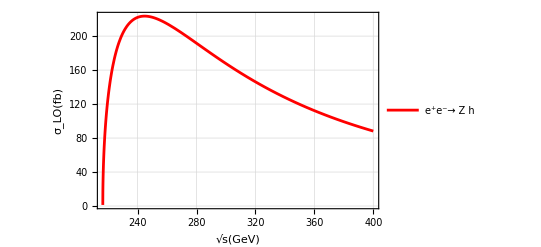

```mathematica
Plot[convfactor σLOSM[s^2],{s,200,400},PlotStyle->{Red},Frame->True,GridLines->Automatic,FrameLabel->{Style["√s(GeV)",FontSize->18,FontFamily->"Times"],Style["σ_LO(fb)",FontSize->18,FontFamily->"Times"]},PlotRange->All,PlotLegends->Placed[{Style["e^+e^-→ Z h",FontFamily->"Times",FontSize->12]},{Right,Top}]]
```

```mathematica
(*ContourPlot takes around 35 minutes to evaluate this plot on a MacBook Pro 2.2 GHz 6-Core Intel Core i7*)
```

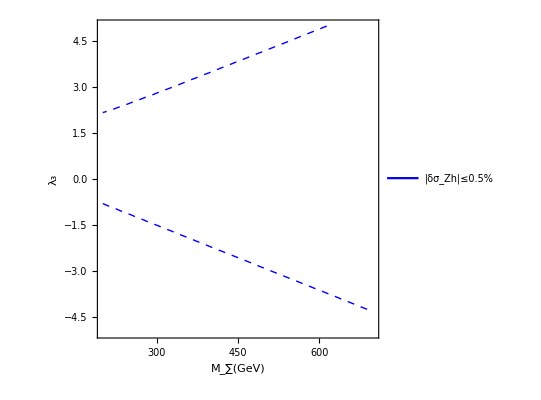

```mathematica
ContourPlot[Abs[σ1loopOS[λ3,MH,MZ,240^2]]/σLOSM[240^2],{MH,200,700},{λ3,-5,5},Contours->{0.5/100},ContourStyle->{{Blue,Dashed}},ContourShading->None,FrameTicksStyle->Directive[Bold,12],FrameLabel->{Style["M_∑(GeV)",FontSize->18,FontFamily->"Times",Bold],Style["λ_3",FontSize->18,FontFamily->"Times",Bold]},PlotLegends->Placed[{Style["|δσ_Zh|≤0.5%",FontFamily->"Times",FontSize->12]},{Left,Bottom}]]
```

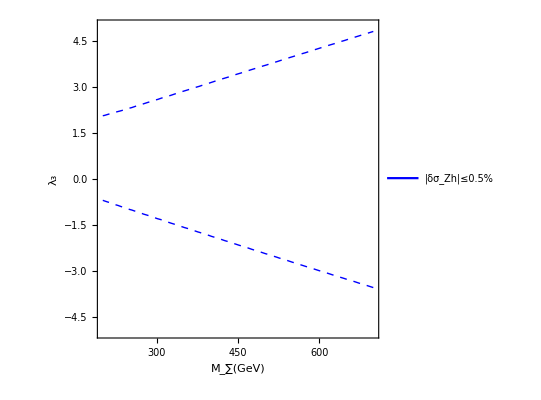

```mathematica
ContourPlot[Abs[σ1loop[λ3,MH,240,240^2]]/σLOSM[240^2],{MH,200,700},{λ3,-5,5},Contours->{0.5/100},ContourStyle->{{Blue,Dashed}},ContourShading->None,FrameTicksStyle->Directive[Bold,12],FrameLabel->{Style["M_∑(GeV)",FontSize->18,FontFamily->"Times",Bold],Style["λ_3",FontSize->18,FontFamily->"Times",Bold]},PlotLegends->Placed[{Style["|δσ_Zh|≤0.5%",FontFamily->"Times",FontSize->12]},{Left,Bottom}]]
```

```mathematica
(*RegionPlot has a bug that does not allow NIntegrate to be evaluated properly, I already tried some solutions on stackexchange but none worked out, https://mathematica.stackexchange.com/questions/94402/error-with-nintegrate-and-regionplot*)
```

```mathematica
(*I have not tried the Plot3D option here though, https://mathematica.stackexchange.com/questions/189717/regionplot-evaluating-nintegrate-before-assigning-variable-values-and-resulting*)
```

```mathematica
(*RegionPlot[ImplicitRegion[(Abs[σ1loop[λ3,MH,MZ,240]]/σLO[240])≤0.005,{{MH,200,700},{λ3,-5,5}}],BoundaryStyle->{Black},PlotRange->{{200,700},{-5,5}},Frame->True,FrameTicksStyle->Directive[Bold,12],FrameLabel->{Style["M_∑(GeV)",FontSize->18,FontFamily->"Times",Bold],Style["λ_3",FontSize->18,FontFamily->"Times",Bold]},
PlotStyle->Directive[Opacity[0.5,Cyan]],PlotLegends->Placed[{Style["|δσ_Zh|≤0.5%",FontFamily->"Times",FontSize->12]},{Left,Bottom}]]*)
```

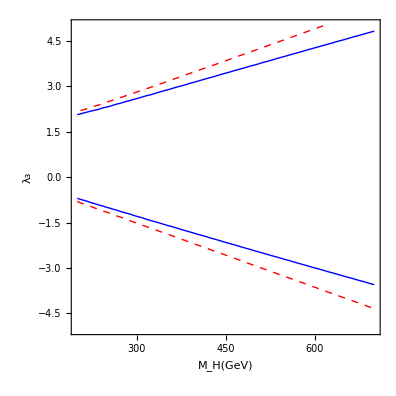

```mathematica
combinedPlot=Show[ContourPlot[Abs[σ1loopOS[λ3,MH,MZ,240^2]]/σLOSM[240^2],{MH,200,700},{λ3,-5,5},Contours->{0.5/100},ContourStyle->{{Red,Thick,Dashed}},ContourShading->None],ContourPlot[Abs[σ1loop[λ3,MH,240,240^2]]/σLOSM[240^2],{MH,200,700},{λ3,-5,5},Contours->{0.5/100},ContourStyle->{{Blue,Thick}},ContourShading->None],FrameTicksStyle->Directive[Bold,12],FrameLabel->{Style["\!\(\*SubscriptBox[\(M\), \(H\)]\)(GeV)",FontSize->18,FontFamily->"Times",Bold],Style["\!\(\*SubscriptBox[\(λ\), \(3\)]\)",FontSize->18,FontFamily->"Times",Bold]},PlotLegends->Placed[LineLegend[{Directive[Red,Thick,Dashed],Directive[Blue,Thick]},{"OS scheme","MS scheme"}],{Left,Top}]]
```